```mathematica
<<TopoTB`
```

## DFT

```mathematica
path=SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
poscar=Import["POSCAR","Table"];
kpoints=Import["KPOINTS","Table"];
eigenval=Import["EIGENVAL","Table"]; 
efermi=-1.7400;
```

```mathematica
DFTds=VASPBand[poscar,kpoints,eigenval,efermi,1,1,"Band.dat"];
```

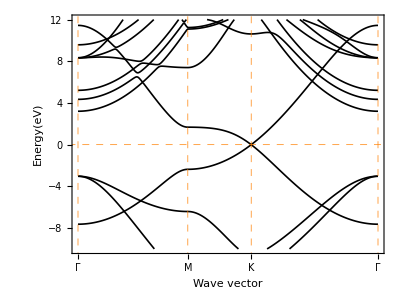

```mathematica
KK=Normal[DFTds[5]];
tband=Normal[DFTds[7]];
DFTfig=BandPlot[tband,KK,Black,0.003,3/4,{-10,12}]
```

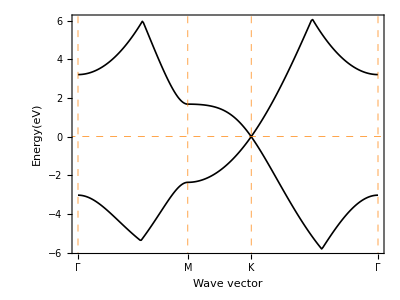

```mathematica
KK=Normal[DFTds[5]];
tband=Normal[DFTds[7]];
BandIndexPlot[{tband[[4]],tband[[5]]},KK,{Black,Black},0.003,3/4,Automatic]
```

## Lattice gauge

```mathematica
poscar
```

{{Graphene},{1.},{1.23211,-2.13409,0.},{1.23211,2.13409,0.},{0.,0.,11.998939846403653},{C},{2},{Direct},{0.,0.,0.5},{0.333333,0.666667,0.5},{},{0.,0.,0.},{0.,0.,0.}}

```mathematica
a=poscar[[3]][[1;;2]]
b=poscar[[4]][[1;;2]]
```

{1.23211,-2.13409}

{1.23211,2.13409}

-Graphics-

```mathematica
k={kx,ky};
(*a={√3,0};b=1/2{-√3,3};*)
(*H={{M,0},{0,-M}}+{{0,t},{t,0}}+
	{{0,0},{0,0}}*Exp[I*k.a]+
	{{0,0},{t,0}}*Exp[I*k.(a+b)]+
	{{0,0},{t,0}}*Exp[I*k.b]+
	{{0,0},{0,0}}*Exp[-I*k.a]+
	{{0,t},{0,0}}*Exp[-I*k.(a+b)]+
	{{0,t},{0,0}}*Exp[-I*k.b];*)
H={{M,0},{0,-M}}+{{0,t},{t,0}}+
	{{0,0},{t,0}}*Exp[I*k.a]+
	{{0,0},{0,0}}*Exp[I*k.(a+b)]+
	{{0,t},{0,0}}*Exp[I*k.b]+
	{{0,t},{0,0}}*Exp[-I*k.a]+
	{{0,0},{0,0}}*Exp[-I*k.(a+b)]+
	{{0,0},{t,0}}*Exp[-I*k.b];
H//TraditionalForm
```

(M | t ⅇ^(-ⅈ (1.23211 kx-2.13409 ky))+t ⅇ^(ⅈ (1.23211 kx+2.13409 ky))+t
t ⅇ^(ⅈ (1.23211 kx-2.13409 ky))+t ⅇ^(-ⅈ (1.23211 kx+2.13409 ky))+t | -M)

```mathematica
lat={a,b};
FBZ2D[lat,False,Blue,Purple,4]
```

```mathematica
poscar[[3;;5]]
```

{{1.23211,-2.13409,0.},{1.23211,2.13409,0.},{0.,0.,11.998939846403653}}

```mathematica
Clear[h]
h[{kx_,ky_,kz_},M_:0,t_:1]=H;
lat=poscar[[3;;5]];
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
ds=HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,0,{1,2},{Red,Blue}]
```

```mathematica
Clear[h]
SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
nband=2;
kpath=Normal[ds[1]];
kdist=Normal[ds[2]];
Manipulate[
	bandFig=Module[{},
		h[{kx_,ky_,kz_},M_:0,t_:1]=H;
		vals=Table[Eigenvalues[h[i,M,t]]//Sort,{i,kpath}];
		band=Table[Transpose[{kdist,vals[[All,i]]}],{i,1,nband}];
		Show[DFTfig,ListLinePlot[band,PlotStyle->Red],PlotLabel->{"M"->ToString[M],"t"->ToString[t]}]
		],
	{M,0,1},{t,-3,3},
	Button["Save and Clear Output",
	fileName="M="<>ToString[M]<>";t="<>ToString[t]<>".png";
	Export[fileName,bandFig];
    NotebookSave[];
    NotebookDelete[EvaluationCell[]]]
	]
```

## Wannier90

```mathematica
SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
wannier90hr=Import["wannier90_hr.dat","Table"];
poscar=Import["POSCAR","Table"];
wfcentre=Import["WFcentre.txt","Table"];
efermi=-1.7400;
lat=poscar[[3;;5]];
```

```mathematica
dsLattice=Wannier90hr[wannier90hr,lat,{kx,ky,kz}]
```

Dataset[<>]

```mathematica
HLattice=Normal[dsLattice[7]];
HLattice//TraditionalForm
HLattice/.{kx->1,ky->1,kz->1}//TraditionalForm
```

(-1.27709+0.2398 ⅇ^((0.-2.46423 ⅈ) kx)+0.2398 ⅇ^((0.+2.46423 ⅈ) kx)-0.010533 ⅇ^((0.-4.92846 ⅈ) kx)-0.010533 ⅇ^((0.+4.92846 ⅈ) kx)-0.003366 ⅇ^((0.-7.39269 ⅈ) kx)-0.003366 ⅇ^((0.+7.39269 ⅈ) kx)-0.000206 ⅇ^((0.-9.85692 ⅈ) kx)-0.000206 ⅇ^((0.+9.85692 ⅈ) kx)-0.000184 ⅇ^((0.-12.3211 ⅈ) kx)-0.000184 ⅇ^((0.+12.3211 ⅈ) kx)+0.000111 ⅇ^((0.-14.7854 ⅈ) kx)+0.000111 ⅇ^((0.+14.7854 ⅈ) kx)+0.000024 ⅇ^((0.-17.2496 ⅈ) kx)+0.000024 ⅇ^((0.+17.2496 ⅈ) kx)-0.000028 ⅇ^((0.-19.7138 ⅈ) kx)-0.000028 ⅇ^((0.+19.7138 ⅈ) kx)+0.0000115 ⅇ^((0.-22.1781 ⅈ) kx)+0.0000115 ⅇ^((0.+22.1781 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.69634 kx-23.4749 ky))-0.000017 ⅇ^(ⅈ (-1.23211 kx-23.4749 ky))-0.000017 ⅇ^(ⅈ (1.23211 kx-23.4749 ky))-0.00001 ⅇ^(ⅈ (3.69634 kx-23.4749 ky))-0.000039 ⅇ^(ⅈ (-7.39269 kx-21.3409 ky))-0.000038 ⅇ^(ⅈ (-4.92846 kx-21.3409 ky))+0.000018 ⅇ^(ⅈ (-2.46423 kx-21.3409 ky))+0.000018 ⅇ^(ⅈ (2.46423 kx-21.3409 ky))-0.000038 ⅇ^(ⅈ (4.92846 kx-21.3409 ky))-0.000039 ⅇ^(ⅈ (7.39269 kx-21.3409 ky))+0.0000115 ⅇ^(ⅈ (-11.089 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (-8.6248 kx-19.2068 ky))+0.000015 ⅇ^(ⅈ (-6.16057 kx-19.2068 ky))+0.000056 ⅇ^(ⅈ (-3.69634 kx-19.2068 ky))+0.00002 ⅇ^(ⅈ (-1.23211 kx-19.2068 ky))+0.00002 ⅇ^(ⅈ (1.23211 kx-19.2068 ky))+0.000056 ⅇ^(ⅈ (3.69634 kx-19.2068 ky))+0.000015 ⅇ^(ⅈ (6.16057 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (8.6248 kx-19.2068 ky))+0.0000115 ⅇ^(ⅈ (11.089 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (-12.3211 kx-17.0727 ky))-0.000028 ⅇ^(ⅈ (-9.85692 kx-17.0727 ky))-0.000061 ⅇ^(ⅈ (-7.39269 kx-17.0727 ky))+0.000022 ⅇ^(ⅈ (-4.92846 kx-17.0727 ky))-0.000072 ⅇ^(ⅈ (-2.46423 kx-17.0727 ky))-0.000072 ⅇ^(ⅈ (2.46423 kx-17.0727 ky))+0.000022 ⅇ^(ⅈ (4.92846 kx-17.0727 ky))-0.000061 ⅇ^(ⅈ (7.39269 kx-17.0727 ky))-0.000028 ⅇ^(ⅈ (9.85692 kx-17.0727 ky))+0.000031 ⅇ^(ⅈ (12.3211 kx-17.0727 ky))-0.000038 ⅇ^(ⅈ (-16.0175 kx-14.9386 ky))-0.000061 ⅇ^(ⅈ (-11.089 kx-14.9386 ky))+0.000024 ⅇ^(ⅈ (-8.6248 kx-14.9386 ky))+0.000081 ⅇ^(ⅈ (-6.16057 kx-14.9386 ky))-0.000022 ⅇ^(ⅈ (-3.69634 kx-14.9386 ky))+0.00005 ⅇ^(ⅈ (-1.23211 kx-14.9386 ky))+0.00005 ⅇ^(ⅈ (1.23211 kx-14.9386 ky))-0.000022 ⅇ^(ⅈ (3.69634 kx-14.9386 ky))+0.000081 ⅇ^(ⅈ (6.16057 kx-14.9386 ky))+0.000024 ⅇ^(ⅈ (8.6248 kx-14.9386 ky))-0.000061 ⅇ^(ⅈ (11.089 kx-14.9386 ky))-0.000038 ⅇ^(ⅈ (16.0175 kx-14.9386 ky))+0.000015 ⅇ^(ⅈ (-13.5533 kx-14.9386 ky))+0.000015 ⅇ^(ⅈ (13.5533 kx-14.9386 ky))-0.000017 ⅇ^(ⅈ (-19.7138 kx-12.8045 ky))-0.000017 ⅇ^(ⅈ (19.7138 kx-12.8045 ky))+0.000019 ⅇ^(ⅈ (-17.2496 kx-12.8045 ky))+0.000022 ⅇ^(ⅈ (-12.3211 kx-12.8045 ky))+0.000081 ⅇ^(ⅈ (-9.85692 kx-12.8045 ky))+0.000111 ⅇ^(ⅈ (-7.39269 kx-12.8045 ky))-0.000084 ⅇ^(ⅈ (-4.92846 kx-12.8045 ky))-0.00009 ⅇ^(ⅈ (-2.46423 kx-12.8045 ky))-0.00009 ⅇ^(ⅈ (2.46423 kx-12.8045 ky))-0.000084 ⅇ^(ⅈ (4.92846 kx-12.8045 ky))+0.000111 ⅇ^(ⅈ (7.39269 kx-12.8045 ky))+0.000081 ⅇ^(ⅈ (9.85692 kx-12.8045 ky))+0.000022 ⅇ^(ⅈ (12.3211 kx-12.8045 ky))+0.000019 ⅇ^(ⅈ (17.2496 kx-12.8045 ky))+0.000056 ⅇ^(ⅈ (-14.7854 kx-12.8045 ky))+0.000056 ⅇ^(ⅈ (14.7854 kx-12.8045 ky))-0.000017 ⅇ^(ⅈ (-20.946 kx-10.6704 ky))-0.000017 ⅇ^(ⅈ (20.946 kx-10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (-18.4817 kx-10.6704 ky))-0.000072 ⅇ^(ⅈ (-13.5533 kx-10.6704 ky))-0.000022 ⅇ^(ⅈ (-11.089 kx-10.6704 ky))-0.000084 ⅇ^(ⅈ (-8.6248 kx-10.6704 ky))-0.000184 ⅇ^(ⅈ (-6.16057 kx-10.6704 ky))-0.000037 ⅇ^(ⅈ (-3.69634 kx-10.6704 ky))-0.000174 ⅇ^(ⅈ (-1.23211 kx-10.6704 ky))-0.000174 ⅇ^(ⅈ (1.23211 kx-10.6704 ky))-0.000037 ⅇ^(ⅈ (3.69634 kx-10.6704 ky))-0.000184 ⅇ^(ⅈ (6.16057 kx-10.6704 ky))-0.000084 ⅇ^(ⅈ (8.6248 kx-10.6704 ky))-0.000022 ⅇ^(ⅈ (11.089 kx-10.6704 ky))-0.000072 ⅇ^(ⅈ (13.5533 kx-10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (18.4817 kx-10.6704 ky))+0.00002 ⅇ^(ⅈ (-16.0175 kx-10.6704 ky))+0.00002 ⅇ^(ⅈ (16.0175 kx-10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (-22.1781 kx-8.53634 ky))-5.×10^-6 ⅇ^(ⅈ (22.1781 kx-8.53634 ky))+0.000018 ⅇ^(ⅈ (-19.7138 kx-8.53634 ky))-0.000035 ⅇ^(ⅈ (-14.7854 kx-8.53634 ky))+0.00005 ⅇ^(ⅈ (-12.3211 kx-8.53634 ky))-0.00009 ⅇ^(ⅈ (-9.85692 kx-8.53634 ky))-0.000037 ⅇ^(ⅈ (-7.39269 kx-8.53634 ky))-0.000206 ⅇ^(ⅈ (-4.92846 kx-8.53634 ky))+0.000848 ⅇ^(ⅈ (-2.46423 kx-8.53634 ky))+0.000848 ⅇ^(ⅈ (2.46423 kx-8.53634 ky))-0.000206 ⅇ^(ⅈ (4.92846 kx-8.53634 ky))-0.000037 ⅇ^(ⅈ (7.39269 kx-8.53634 ky))-0.00009 ⅇ^(ⅈ (9.85692 kx-8.53634 ky))+0.00005 ⅇ^(ⅈ (12.3211 kx-8.53634 ky))-0.000035 ⅇ^(ⅈ (14.7854 kx-8.53634 ky))+0.000018 ⅇ^(ⅈ (19.7138 kx-8.53634 ky))+0.00002 ⅇ^(ⅈ (-17.2496 kx-8.53634 ky))+0.00002 ⅇ^(ⅈ (17.2496 kx-8.53634 ky))-0.000038 ⅇ^(ⅈ (-20.946 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (-16.0175 kx-6.40226 ky))+0.00005 ⅇ^(ⅈ (-13.5533 kx-6.40226 ky))+0.000133 ⅇ^(ⅈ (-11.089 kx-6.40226 ky))-0.000174 ⅇ^(ⅈ (-8.6248 kx-6.40226 ky))+0.000848 ⅇ^(ⅈ (-6.16057 kx-6.40226 ky))-0.003366 ⅇ^(ⅈ (-3.69634 kx-6.40226 ky))+0.004122 ⅇ^(ⅈ (-1.23211 kx-6.40226 ky))+0.004122 ⅇ^(ⅈ (1.23211 kx-6.40226 ky))-0.003366 ⅇ^(ⅈ (3.69634 kx-6.40226 ky))+0.000848 ⅇ^(ⅈ (6.16057 kx-6.40226 ky))-0.000174 ⅇ^(ⅈ (8.6248 kx-6.40226 ky))+0.000133 ⅇ^(ⅈ (11.089 kx-6.40226 ky))+0.00005 ⅇ^(ⅈ (13.5533 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (16.0175 kx-6.40226 ky))-0.000038 ⅇ^(ⅈ (20.946 kx-6.40226 ky))+0.000056 ⅇ^(ⅈ (-18.4817 kx-6.40226 ky))+0.000056 ⅇ^(ⅈ (18.4817 kx-6.40226 ky))-0.0000195 ⅇ^(ⅈ (-22.1781 kx-4.26817 ky))+0.000022 ⅇ^(ⅈ (-17.2496 kx-4.26817 ky))-0.000022 ⅇ^(ⅈ (-14.7854 kx-4.26817 ky))-0.00009 ⅇ^(ⅈ (-12.3211 kx-4.26817 ky))-0.000174 ⅇ^(ⅈ (-9.85692 kx-4.26817 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.39269 kx-4.26817 ky))+0.004122 ⅇ^(ⅈ (-4.92846 kx-4.26817 ky))-0.010533 ⅇ^(ⅈ (-2.46423 kx-4.26817 ky))-0.010533 ⅇ^(ⅈ (2.46423 kx-4.26817 ky))+0.004122 ⅇ^(ⅈ (4.92846 kx-4.26817 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.39269 kx-4.26817 ky))-0.000174 ⅇ^(ⅈ (9.85692 kx-4.26817 ky))-0.00009 ⅇ^(ⅈ (12.3211 kx-4.26817 ky))-0.000022 ⅇ^(ⅈ (14.7854 kx-4.26817 ky))+0.000022 ⅇ^(ⅈ (17.2496 kx-4.26817 ky))-0.0000195 ⅇ^(ⅈ (22.1781 kx-4.26817 ky))+0.000015 ⅇ^(ⅈ (-19.7138 kx-4.26817 ky))+0.000015 ⅇ^(ⅈ (19.7138 kx-4.26817 ky))-0.000061 ⅇ^(ⅈ (-18.4817 kx-2.13409 ky))+0.000081 ⅇ^(ⅈ (-16.0175 kx-2.13409 ky))-0.000084 ⅇ^(ⅈ (-13.5533 kx-2.13409 ky))-0.000037 ⅇ^(ⅈ (-11.089 kx-2.13409 ky))+0.000848 ⅇ^(ⅈ (-8.6248 kx-2.13409 ky))+0.004122 ⅇ^(ⅈ (-6.16057 kx-2.13409 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.69634 kx-2.13409 ky))+0.239801 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky))+0.239801 ⅇ^(ⅈ (1.23211 kx-2.13409 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.69634 kx-2.13409 ky))+0.004122 ⅇ^(ⅈ (6.16057 kx-2.13409 ky))+0.000848 ⅇ^(ⅈ (8.6248 kx-2.13409 ky))-0.000037 ⅇ^(ⅈ (11.089 kx-2.13409 ky))-0.000084 ⅇ^(ⅈ (13.5533 kx-2.13409 ky))+0.000081 ⅇ^(ⅈ (16.0175 kx-2.13409 ky))-0.000061 ⅇ^(ⅈ (18.4817 kx-2.13409 ky))+0.000031 ⅇ^(ⅈ (-20.946 kx-2.13409 ky))+0.000031 ⅇ^(ⅈ (20.946 kx-2.13409 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.26817 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.26817 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.53634 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.53634 ⅈ) ky)+0.000133 ⅇ^((0.-12.8045 ⅈ) ky)+0.000133 ⅇ^((0.+12.8045 ⅈ) ky)-0.000035 ⅇ^((0.-17.0727 ⅈ) ky)-0.000035 ⅇ^((0.+17.0727 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3409 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3409 ⅈ) ky)+0.000052 ⅇ^((0.-25.609 ⅈ) ky)+0.000052 ⅇ^((0.+25.609 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13409 ky-20.946 kx))+0.000031 ⅇ^(ⅈ (20.946 kx+2.13409 ky))-0.000061 ⅇ^(ⅈ (2.13409 ky-18.4817 kx))+0.000081 ⅇ^(ⅈ (2.13409 ky-16.0175 kx))-0.000084 ⅇ^(ⅈ (2.13409 ky-13.5533 kx))-0.000037 ⅇ^(ⅈ (2.13409 ky-11.089 kx))+0.000848 ⅇ^(ⅈ (2.13409 ky-8.6248 kx))+0.004122 ⅇ^(ⅈ (2.13409 ky-6.16057 kx))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13409 ky-3.69634 kx))+0.239801 ⅇ^(ⅈ (2.13409 ky-1.23211 kx))+0.239801 ⅇ^(ⅈ (1.23211 kx+2.13409 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.69634 kx+2.13409 ky))+0.004122 ⅇ^(ⅈ (6.16057 kx+2.13409 ky))+0.000848 ⅇ^(ⅈ (8.6248 kx+2.13409 ky))-0.000037 ⅇ^(ⅈ (11.089 kx+2.13409 ky))-0.000084 ⅇ^(ⅈ (13.5533 kx+2.13409 ky))+0.000081 ⅇ^(ⅈ (16.0175 kx+2.13409 ky))-0.000061 ⅇ^(ⅈ (18.4817 kx+2.13409 ky))+0.000015 ⅇ^(ⅈ (4.26817 ky-19.7138 kx))+0.000015 ⅇ^(ⅈ (19.7138 kx+4.26817 ky))-0.0000195 ⅇ^(ⅈ (4.26817 ky-22.1781 kx))+0.000022 ⅇ^(ⅈ (4.26817 ky-17.2496 kx))-0.000022 ⅇ^(ⅈ (4.26817 ky-14.7854 kx))-0.00009 ⅇ^(ⅈ (4.26817 ky-12.3211 kx))-0.000174 ⅇ^(ⅈ (4.26817 ky-9.85692 kx))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.26817 ky-7.39269 kx))+0.004122 ⅇ^(ⅈ (4.26817 ky-4.92846 kx))-0.010533 ⅇ^(ⅈ (4.26817 ky-2.46423 kx))-0.010533 ⅇ^(ⅈ (2.46423 kx+4.26817 ky))+0.004122 ⅇ^(ⅈ (4.92846 kx+4.26817 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.39269 kx+4.26817 ky))-0.000174 ⅇ^(ⅈ (9.85692 kx+4.26817 ky))-0.00009 ⅇ^(ⅈ (12.3211 kx+4.26817 ky))-0.000022 ⅇ^(ⅈ (14.7854 kx+4.26817 ky))+0.000022 ⅇ^(ⅈ (17.2496 kx+4.26817 ky))-0.0000195 ⅇ^(ⅈ (22.1781 kx+4.26817 ky))+0.000056 ⅇ^(ⅈ (6.40226 ky-18.4817 kx))+0.000056 ⅇ^(ⅈ (18.4817 kx+6.40226 ky))-0.000038 ⅇ^(ⅈ (6.40226 ky-20.946 kx))-0.000072 ⅇ^(ⅈ (6.40226 ky-16.0175 kx))+0.00005 ⅇ^(ⅈ (6.40226 ky-13.5533 kx))+0.000133 ⅇ^(ⅈ (6.40226 ky-11.089 kx))-0.000174 ⅇ^(ⅈ (6.40226 ky-8.6248 kx))+0.000848 ⅇ^(ⅈ (6.40226 ky-6.16057 kx))-0.003366 ⅇ^(ⅈ (6.40226 ky-3.69634 kx))+0.004122 ⅇ^(ⅈ (6.40226 ky-1.23211 kx))+0.004122 ⅇ^(ⅈ (1.23211 kx+6.40226 ky))-0.003366 ⅇ^(ⅈ (3.69634 kx+6.40226 ky))+0.000848 ⅇ^(ⅈ (6.16057 kx+6.40226 ky))-0.000174 ⅇ^(ⅈ (8.6248 kx+6.40226 ky))+0.000133 ⅇ^(ⅈ (11.089 kx+6.40226 ky))+0.00005 ⅇ^(ⅈ (13.5533 kx+6.40226 ky))-0.000072 ⅇ^(ⅈ (16.0175 kx+6.40226 ky))-0.000038 ⅇ^(ⅈ (20.946 kx+6.40226 ky))+0.00002 ⅇ^(ⅈ (8.53634 ky-17.2496 kx))+0.00002 ⅇ^(ⅈ (17.2496 kx+8.53634 ky))+0.000018 ⅇ^(ⅈ (8.53634 ky-19.7138 kx))-0.000035 ⅇ^(ⅈ (8.53634 ky-14.7854 kx))+0.00005 ⅇ^(ⅈ (8.53634 ky-12.3211 kx))-0.00009 ⅇ^(ⅈ (8.53634 ky-9.85692 kx))-0.000037 ⅇ^(ⅈ (8.53634 ky-7.39269 kx))-0.000206 ⅇ^(ⅈ (8.53634 ky-4.92846 kx))+0.000848 ⅇ^(ⅈ (8.53634 ky-2.46423 kx))+0.000848 ⅇ^(ⅈ (2.46423 kx+8.53634 ky))-0.000206 ⅇ^(ⅈ (4.92846 kx+8.53634 ky))-0.000037 ⅇ^(ⅈ (7.39269 kx+8.53634 ky))-0.00009 ⅇ^(ⅈ (9.85692 kx+8.53634 ky))+0.00005 ⅇ^(ⅈ (12.3211 kx+8.53634 ky))-0.000035 ⅇ^(ⅈ (14.7854 kx+8.53634 ky))+0.000018 ⅇ^(ⅈ (19.7138 kx+8.53634 ky))-5.×10^-6 ⅇ^(ⅈ (8.53634 ky-22.1781 kx))-5.×10^-6 ⅇ^(ⅈ (22.1781 kx+8.53634 ky))+0.00002 ⅇ^(ⅈ (10.6704 ky-16.0175 kx))+0.00002 ⅇ^(ⅈ (16.0175 kx+10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (10.6704 ky-18.4817 kx))-0.000072 ⅇ^(ⅈ (10.6704 ky-13.5533 kx))-0.000022 ⅇ^(ⅈ (10.6704 ky-11.089 kx))-0.000084 ⅇ^(ⅈ (10.6704 ky-8.6248 kx))-0.000184 ⅇ^(ⅈ (10.6704 ky-6.16057 kx))-0.000037 ⅇ^(ⅈ (10.6704 ky-3.69634 kx))-0.000174 ⅇ^(ⅈ (10.6704 ky-1.23211 kx))-0.000174 ⅇ^(ⅈ (1.23211 kx+10.6704 ky))-0.000037 ⅇ^(ⅈ (3.69634 kx+10.6704 ky))-0.000184 ⅇ^(ⅈ (6.16057 kx+10.6704 ky))-0.000084 ⅇ^(ⅈ (8.6248 kx+10.6704 ky))-0.000022 ⅇ^(ⅈ (11.089 kx+10.6704 ky))-0.000072 ⅇ^(ⅈ (13.5533 kx+10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (18.4817 kx+10.6704 ky))-0.000017 ⅇ^(ⅈ (10.6704 ky-20.946 kx))-0.000017 ⅇ^(ⅈ (20.946 kx+10.6704 ky))+0.000056 ⅇ^(ⅈ (12.8045 ky-14.7854 kx))+0.000056 ⅇ^(ⅈ (14.7854 kx+12.8045 ky))+0.000019 ⅇ^(ⅈ (12.8045 ky-17.2496 kx))+0.000022 ⅇ^(ⅈ (12.8045 ky-12.3211 kx))+0.000081 ⅇ^(ⅈ (12.8045 ky-9.85692 kx))+0.000111 ⅇ^(ⅈ (12.8045 ky-7.39269 kx))-0.000084 ⅇ^(ⅈ (12.8045 ky-4.92846 kx))-0.00009 ⅇ^(ⅈ (12.8045 ky-2.46423 kx))-0.00009 ⅇ^(ⅈ (2.46423 kx+12.8045 ky))-0.000084 ⅇ^(ⅈ (4.92846 kx+12.8045 ky))+0.000111 ⅇ^(ⅈ (7.39269 kx+12.8045 ky))+0.000081 ⅇ^(ⅈ (9.85692 kx+12.8045 ky))+0.000022 ⅇ^(ⅈ (12.3211 kx+12.8045 ky))+0.000019 ⅇ^(ⅈ (17.2496 kx+12.8045 ky))-0.000017 ⅇ^(ⅈ (12.8045 ky-19.7138 kx))-0.000017 ⅇ^(ⅈ (19.7138 kx+12.8045 ky))+0.000015 ⅇ^(ⅈ (14.9386 ky-13.5533 kx))+0.000015 ⅇ^(ⅈ (13.5533 kx+14.9386 ky))-0.000038 ⅇ^(ⅈ (14.9386 ky-16.0175 kx))-0.000061 ⅇ^(ⅈ (14.9386 ky-11.089 kx))+0.000024 ⅇ^(ⅈ (14.9386 ky-8.6248 kx))+0.000081 ⅇ^(ⅈ (14.9386 ky-6.16057 kx))-0.000022 ⅇ^(ⅈ (14.9386 ky-3.69634 kx))+0.00005 ⅇ^(ⅈ (14.9386 ky-1.23211 kx))+0.00005 ⅇ^(ⅈ (1.23211 kx+14.9386 ky))-0.000022 ⅇ^(ⅈ (3.69634 kx+14.9386 ky))+0.000081 ⅇ^(ⅈ (6.16057 kx+14.9386 ky))+0.000024 ⅇ^(ⅈ (8.6248 kx+14.9386 ky))-0.000061 ⅇ^(ⅈ (11.089 kx+14.9386 ky))-0.000038 ⅇ^(ⅈ (16.0175 kx+14.9386 ky))+0.000031 ⅇ^(ⅈ (17.0727 ky-12.3211 kx))-0.000028 ⅇ^(ⅈ (17.0727 ky-9.85692 kx))-0.000061 ⅇ^(ⅈ (17.0727 ky-7.39269 kx))+0.000022 ⅇ^(ⅈ (17.0727 ky-4.92846 kx))-0.000072 ⅇ^(ⅈ (17.0727 ky-2.46423 kx))-0.000072 ⅇ^(ⅈ (2.46423 kx+17.0727 ky))+0.000022 ⅇ^(ⅈ (4.92846 kx+17.0727 ky))-0.000061 ⅇ^(ⅈ (7.39269 kx+17.0727 ky))-0.000028 ⅇ^(ⅈ (9.85692 kx+17.0727 ky))+0.000031 ⅇ^(ⅈ (12.3211 kx+17.0727 ky))+0.0000115 ⅇ^(ⅈ (19.2068 ky-11.089 kx))+0.000031 ⅇ^(ⅈ (19.2068 ky-8.6248 kx))+0.000015 ⅇ^(ⅈ (19.2068 ky-6.16057 kx))+0.000056 ⅇ^(ⅈ (19.2068 ky-3.69634 kx))+0.00002 ⅇ^(ⅈ (19.2068 ky-1.23211 kx))+0.00002 ⅇ^(ⅈ (1.23211 kx+19.2068 ky))+0.000056 ⅇ^(ⅈ (3.69634 kx+19.2068 ky))+0.000015 ⅇ^(ⅈ (6.16057 kx+19.2068 ky))+0.000031 ⅇ^(ⅈ (8.6248 kx+19.2068 ky))+0.0000115 ⅇ^(ⅈ (11.089 kx+19.2068 ky))-0.000039 ⅇ^(ⅈ (21.3409 ky-7.39269 kx))-0.000038 ⅇ^(ⅈ (21.3409 ky-4.92846 kx))+0.000018 ⅇ^(ⅈ (21.3409 ky-2.46423 kx))+0.000018 ⅇ^(ⅈ (2.46423 kx+21.3409 ky))-0.000038 ⅇ^(ⅈ (4.92846 kx+21.3409 ky))-0.000039 ⅇ^(ⅈ (7.39269 kx+21.3409 ky))-0.00001 ⅇ^(ⅈ (23.4749 ky-3.69634 kx))-0.000017 ⅇ^(ⅈ (23.4749 ky-1.23211 kx))-0.000017 ⅇ^(ⅈ (1.23211 kx+23.4749 ky))-0.00001 ⅇ^(ⅈ (3.69634 kx+23.4749 ky)) | -2.82749-0.215067 ⅇ^((0.-2.46423 ⅈ) kx)-0.215067 ⅇ^((0.+2.46423 ⅈ) kx)-0.011301 ⅇ^((0.-4.92846 ⅈ) kx)-0.011301 ⅇ^((0.+4.92846 ⅈ) kx)+0.000371 ⅇ^((0.-7.39269 ⅈ) kx)+0.000371 ⅇ^((0.+7.39269 ⅈ) kx)-0.000142 ⅇ^((0.-9.85692 ⅈ) kx)-0.000143 ⅇ^((0.+9.85692 ⅈ) kx)+0.000273 ⅇ^((0.-12.3211 ⅈ) kx)+0.000274 ⅇ^((0.+12.3211 ⅈ) kx)-0.000133 ⅇ^((0.-14.7854 ⅈ) kx)-0.000133 ⅇ^((0.+14.7854 ⅈ) kx)+0.000039 ⅇ^((0.-17.2496 ⅈ) kx)+0.000039 ⅇ^((0.+17.2496 ⅈ) kx)+0.000082 ⅇ^((0.-19.7138 ⅈ) kx)+0.000082 ⅇ^((0.+19.7138 ⅈ) kx)-0.0000565 ⅇ^((0.-22.1781 ⅈ) kx)-0.0000565 ⅇ^((0.+22.1781 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.69634 kx-23.4749 ky))-0.000018 ⅇ^(ⅈ (-1.23211 kx-23.4749 ky))-0.000018 ⅇ^(ⅈ (1.23211 kx-23.4749 ky))-9.×10^-6 ⅇ^(ⅈ (3.69634 kx-23.4749 ky))+0.000031 ⅇ^(ⅈ (-7.39269 kx-21.3409 ky))+0.000079 ⅇ^(ⅈ (-4.92846 kx-21.3409 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46423 kx-21.3409 ky))-9.×10^-6 ⅇ^(ⅈ (2.46423 kx-21.3409 ky))+0.000079 ⅇ^(ⅈ (4.92846 kx-21.3409 ky))+0.000031 ⅇ^(ⅈ (7.39269 kx-21.3409 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.089 kx-19.2068 ky))+0.000045 ⅇ^(ⅈ (-8.6248 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (-6.16057 kx-19.2068 ky))-0.000039 ⅇ^(ⅈ (-3.69634 kx-19.2068 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23211 kx-19.2068 ky))-5.×10^-6 ⅇ^(ⅈ (1.23211 kx-19.2068 ky))-0.000039 ⅇ^(ⅈ (3.69634 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (6.16057 kx-19.2068 ky))+0.000045 ⅇ^(ⅈ (8.6248 kx-19.2068 ky))-7.5×10^-6 ⅇ^(ⅈ (11.089 kx-19.2068 ky))-0.000113 ⅇ^(ⅈ (-12.3211 kx-17.0727 ky))-0.000015 ⅇ^(ⅈ (-9.85692 kx-17.0727 ky))-0.000038 ⅇ^(ⅈ (-7.39269 kx-17.0727 ky))-0.00011 ⅇ^(ⅈ (-4.92846 kx-17.0727 ky))-0.00002 ⅇ^(ⅈ (-2.46423 kx-17.0727 ky))-0.00002 ⅇ^(ⅈ (2.46423 kx-17.0727 ky))-0.00011 ⅇ^(ⅈ (4.92846 kx-17.0727 ky))-0.000038 ⅇ^(ⅈ (7.39269 kx-17.0727 ky))-0.000015 ⅇ^(ⅈ (9.85692 kx-17.0727 ky))-0.000113 ⅇ^(ⅈ (12.3211 kx-17.0727 ky))-0.000047 ⅇ^(ⅈ (-16.0175 kx-14.9386 ky))+0.000082 ⅇ^(ⅈ (-11.089 kx-14.9386 ky))+0.000027 ⅇ^(ⅈ (-8.6248 kx-14.9386 ky))+0.000031 ⅇ^(ⅈ (-6.16057 kx-14.9386 ky))+0.000182 ⅇ^(ⅈ (-3.69634 kx-14.9386 ky))+0.000057 ⅇ^(ⅈ (-1.23211 kx-14.9386 ky))+0.000057 ⅇ^(ⅈ (1.23211 kx-14.9386 ky))+0.000182 ⅇ^(ⅈ (3.69634 kx-14.9386 ky))+0.000031 ⅇ^(ⅈ (6.16057 kx-14.9386 ky))+0.000027 ⅇ^(ⅈ (8.6248 kx-14.9386 ky))+0.000082 ⅇ^(ⅈ (11.089 kx-14.9386 ky))-0.000047 ⅇ^(ⅈ (16.0175 kx-14.9386 ky))-0.000036 ⅇ^(ⅈ (-13.5533 kx-14.9386 ky))-0.000036 ⅇ^(ⅈ (13.5533 kx-14.9386 ky))+1.×10^-6 ⅇ^(ⅈ (19.7138 kx-12.8045 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2496 kx-12.8045 ky))+0.000046 ⅇ^(ⅈ (-12.3211 kx-12.8045 ky))+0.000039 ⅇ^(ⅈ (-9.85692 kx-12.8045 ky))+0.000015 ⅇ^(ⅈ (-7.39269 kx-12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (-4.92846 kx-12.8045 ky))-0.000167 ⅇ^(ⅈ (-2.46423 kx-12.8045 ky))-0.000167 ⅇ^(ⅈ (2.46423 kx-12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (4.92846 kx-12.8045 ky))+0.000015 ⅇ^(ⅈ (7.39269 kx-12.8045 ky))+0.000039 ⅇ^(ⅈ (9.85692 kx-12.8045 ky))+0.000046 ⅇ^(ⅈ (12.3211 kx-12.8045 ky))-6.×10^-6 ⅇ^(ⅈ (17.2496 kx-12.8045 ky))+0.000043 ⅇ^(ⅈ (-14.7854 kx-12.8045 ky))+0.000043 ⅇ^(ⅈ (14.7854 kx-12.8045 ky))-0.000013 ⅇ^(ⅈ (-20.946 kx-10.6704 ky))-0.000013 ⅇ^(ⅈ (20.946 kx-10.6704 ky))+0.000015 ⅇ^(ⅈ (-18.4817 kx-10.6704 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5533 kx-10.6704 ky))-0.00005 ⅇ^(ⅈ (-11.089 kx-10.6704 ky))-0.000133 ⅇ^(ⅈ (-8.6248 kx-10.6704 ky))-0.000081 ⅇ^(ⅈ (-6.16057 kx-10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (-3.69634 kx-10.6704 ky))+0.000027 ⅇ^(ⅈ (-1.23211 kx-10.6704 ky))+0.000027 ⅇ^(ⅈ (1.23211 kx-10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (3.69634 kx-10.6704 ky))-0.000081 ⅇ^(ⅈ (6.16057 kx-10.6704 ky))-0.000133 ⅇ^(ⅈ (8.6248 kx-10.6704 ky))-0.00005 ⅇ^(ⅈ (11.089 kx-10.6704 ky))+8.×10^-6 ⅇ^(ⅈ (13.5533 kx-10.6704 ky))+0.000015 ⅇ^(ⅈ (18.4817 kx-10.6704 ky))-0.000026 ⅇ^(ⅈ (-16.0175 kx-10.6704 ky))-0.000026 ⅇ^(ⅈ (16.0175 kx-10.6704 ky))+0.000015 ⅇ^(ⅈ (-19.7138 kx-8.53634 ky))+0.000045 ⅇ^(ⅈ (-14.7854 kx-8.53634 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3211 kx-8.53634 ky))+0.000039 ⅇ^(ⅈ (-9.85692 kx-8.53634 ky))+0.000273 ⅇ^(ⅈ (-7.39269 kx-8.53634 ky))+0.000077 ⅇ^(ⅈ (-4.92846 kx-8.53634 ky))-0.000211 ⅇ^(ⅈ (-2.46423 kx-8.53634 ky))-0.000211 ⅇ^(ⅈ (2.46423 kx-8.53634 ky))+0.000077 ⅇ^(ⅈ (4.92846 kx-8.53634 ky))+0.000273 ⅇ^(ⅈ (7.39269 kx-8.53634 ky))+0.000039 ⅇ^(ⅈ (9.85692 kx-8.53634 ky))+2.×10^-6 ⅇ^(ⅈ (12.3211 kx-8.53634 ky))+0.000045 ⅇ^(ⅈ (14.7854 kx-8.53634 ky))+0.000015 ⅇ^(ⅈ (19.7138 kx-8.53634 ky))+0.000021 ⅇ^(ⅈ (-17.2496 kx-8.53634 ky))+0.000021 ⅇ^(ⅈ (17.2496 kx-8.53634 ky))-6.×10^-6 ⅇ^(ⅈ (-20.946 kx-6.40226 ky))+0.000045 ⅇ^(ⅈ (-16.0175 kx-6.40226 ky))-0.000036 ⅇ^(ⅈ (-13.5533 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (-11.089 kx-6.40226 ky))-0.000031 ⅇ^(ⅈ (-8.6248 kx-6.40226 ky))-0.000142 ⅇ^(ⅈ (-6.16057 kx-6.40226 ky))+0.000689 ⅇ^(ⅈ (-3.69634 kx-6.40226 ky))-0.002413 ⅇ^(ⅈ (-1.23211 kx-6.40226 ky))-0.002413 ⅇ^(ⅈ (1.23211 kx-6.40226 ky))+0.000689 ⅇ^(ⅈ (3.69634 kx-6.40226 ky))-0.000142 ⅇ^(ⅈ (6.16057 kx-6.40226 ky))-0.000031 ⅇ^(ⅈ (8.6248 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (11.089 kx-6.40226 ky))-0.000036 ⅇ^(ⅈ (13.5533 kx-6.40226 ky))+0.000045 ⅇ^(ⅈ (16.0175 kx-6.40226 ky))-6.×10^-6 ⅇ^(ⅈ (20.946 kx-6.40226 ky))-0.000026 ⅇ^(ⅈ (-18.4817 kx-6.40226 ky))-0.000026 ⅇ^(ⅈ (18.4817 kx-6.40226 ky))-0.0000235 ⅇ^(ⅈ (-22.1781 kx-4.26817 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2496 kx-4.26817 ky))+2.×10^-6 ⅇ^(ⅈ (-14.7854 kx-4.26817 ky))-0.000072 ⅇ^(ⅈ (-12.3211 kx-4.26817 ky))-0.000236 ⅇ^(ⅈ (-9.85692 kx-4.26817 ky))-0.000343 ⅇ^(ⅈ (-7.39269 kx-4.26817 ky))+0.000371 ⅇ^(ⅈ (-4.92846 kx-4.26817 ky))+0.009282 ⅇ^(ⅈ (-2.46423 kx-4.26817 ky))+0.009282 ⅇ^(ⅈ (2.46423 kx-4.26817 ky))+0.000371 ⅇ^(ⅈ (4.92846 kx-4.26817 ky))-0.000343 ⅇ^(ⅈ (7.39269 kx-4.26817 ky))-0.000236 ⅇ^(ⅈ (9.85692 kx-4.26817 ky))-0.000072 ⅇ^(ⅈ (12.3211 kx-4.26817 ky))+2.×10^-6 ⅇ^(ⅈ (14.7854 kx-4.26817 ky))+8.×10^-6 ⅇ^(ⅈ (17.2496 kx-4.26817 ky))-0.0000235 ⅇ^(ⅈ (22.1781 kx-4.26817 ky))+0.000043 ⅇ^(ⅈ (-19.7138 kx-4.26817 ky))+0.000043 ⅇ^(ⅈ (19.7138 kx-4.26817 ky))+0.000046 ⅇ^(ⅈ (-18.4817 kx-2.13409 ky))-0.00005 ⅇ^(ⅈ (-16.0175 kx-2.13409 ky))+0.000039 ⅇ^(ⅈ (-13.5533 kx-2.13409 ky))-0.000031 ⅇ^(ⅈ (-11.089 kx-2.13409 ky))-0.000343 ⅇ^(ⅈ (-8.6248 kx-2.13409 ky))-0.001909 ⅇ^(ⅈ (-6.16057 kx-2.13409 ky))-0.011301 ⅇ^(ⅈ (-3.69634 kx-2.13409 ky))-0.004839 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky))-0.004839 ⅇ^(ⅈ (1.23211 kx-2.13409 ky))-0.011301 ⅇ^(ⅈ (3.69634 kx-2.13409 ky))-0.001909 ⅇ^(ⅈ (6.16057 kx-2.13409 ky))-0.000343 ⅇ^(ⅈ (8.6248 kx-2.13409 ky))-0.000031 ⅇ^(ⅈ (11.089 kx-2.13409 ky))+0.000039 ⅇ^(ⅈ (13.5533 kx-2.13409 ky))-0.00005 ⅇ^(ⅈ (16.0175 kx-2.13409 ky))+0.000046 ⅇ^(ⅈ (18.4817 kx-2.13409 ky))-0.000036 ⅇ^(ⅈ (-20.946 kx-2.13409 ky))-0.000036 ⅇ^(ⅈ (20.946 kx-2.13409 ky))-0.013694 ⅇ^((0.-4.26817 ⅈ) ky)-0.215067 ⅇ^((0.+4.26817 ⅈ) ky)+0.00057 ⅇ^((0.-8.53634 ⅈ) ky)-0.001909 ⅇ^((0.+8.53634 ⅈ) ky)-0.000312 ⅇ^((0.-12.8045 ⅈ) ky)-0.000236 ⅇ^((0.+12.8045 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.0727 ⅈ) ky)-0.000036 ⅇ^((0.+17.0727 ⅈ) ky)+0.000066 ⅇ^((0.-21.3409 ⅈ) ky)+0.000021 ⅇ^((0.+21.3409 ⅈ) ky)-0.000018 ⅇ^((0.-25.609 ⅈ) ky)-0.000013 ⅇ^((0.+25.609 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13409 ky-20.946 kx))-0.000015 ⅇ^(ⅈ (20.946 kx+2.13409 ky))+0.000027 ⅇ^(ⅈ (2.13409 ky-18.4817 kx))+0.000015 ⅇ^(ⅈ (2.13409 ky-16.0175 kx))-0.000081 ⅇ^(ⅈ (2.13409 ky-13.5533 kx))+0.000077 ⅇ^(ⅈ (2.13409 ky-11.089 kx))+0.000689 ⅇ^(ⅈ (2.13409 ky-8.6248 kx))+0.009282 ⅇ^(ⅈ (2.13409 ky-6.16057 kx))-0.004839 ⅇ^(ⅈ (2.13409 ky-3.69634 kx))-2.82749 ⅇ^(ⅈ (2.13409 ky-1.23211 kx))-2.82749 ⅇ^(ⅈ (1.23211 kx+2.13409 ky))-0.004839 ⅇ^(ⅈ (3.69634 kx+2.13409 ky))+0.009282 ⅇ^(ⅈ (6.16057 kx+2.13409 ky))+0.000689 ⅇ^(ⅈ (8.6248 kx+2.13409 ky))+0.000077 ⅇ^(ⅈ (11.089 kx+2.13409 ky))-0.000081 ⅇ^(ⅈ (13.5533 kx+2.13409 ky))+0.000016 ⅇ^(ⅈ (16.0175 kx+2.13409 ky))+0.000027 ⅇ^(ⅈ (18.4817 kx+2.13409 ky))-0.000038 ⅇ^(ⅈ (4.26817 ky-19.7138 kx))-0.000038 ⅇ^(ⅈ (19.7138 kx+4.26817 ky))+0.0000225 ⅇ^(ⅈ (4.26817 ky-22.1781 kx))+0.000031 ⅇ^(ⅈ (4.26817 ky-17.2496 kx))-2.×10^-6 ⅇ^(ⅈ (4.26817 ky-14.7854 kx))+7.×10^-6 ⅇ^(ⅈ (4.26817 ky-12.3211 kx))-0.000211 ⅇ^(ⅈ (4.26817 ky-9.85692 kx))-0.002413 ⅇ^(ⅈ (4.26817 ky-7.39269 kx))-0.013694 ⅇ^(ⅈ (4.26817 ky-4.92846 kx))-0.004839 ⅇ^(ⅈ (4.26817 ky-2.46423 kx))-0.004839 ⅇ^(ⅈ (2.46423 kx+4.26817 ky))-0.013694 ⅇ^(ⅈ (4.92846 kx+4.26817 ky))-0.002413 ⅇ^(ⅈ (7.39269 kx+4.26817 ky))-0.000211 ⅇ^(ⅈ (9.85692 kx+4.26817 ky))+7.×10^-6 ⅇ^(ⅈ (12.3211 kx+4.26817 ky))-2.×10^-6 ⅇ^(ⅈ (14.7854 kx+4.26817 ky))+0.000031 ⅇ^(ⅈ (17.2496 kx+4.26817 ky))+0.0000225 ⅇ^(ⅈ (22.1781 kx+4.26817 ky))-0.00011 ⅇ^(ⅈ (6.40226 ky-18.4817 kx))-0.00011 ⅇ^(ⅈ (18.4817 kx+6.40226 ky))+0.000031 ⅇ^(ⅈ (6.40226 ky-20.946 kx))+0.000182 ⅇ^(ⅈ (6.40226 ky-16.0175 kx))-0.000167 ⅇ^(ⅈ (6.40226 ky-13.5533 kx))+0.000027 ⅇ^(ⅈ (6.40226 ky-11.089 kx))+0.00057 ⅇ^(ⅈ (6.40226 ky-8.6248 kx))-0.002413 ⅇ^(ⅈ (6.40226 ky-6.16057 kx))+0.009282 ⅇ^(ⅈ (6.40226 ky-3.69634 kx))-0.011301 ⅇ^(ⅈ (6.40226 ky-1.23211 kx))-0.011301 ⅇ^(ⅈ (1.23211 kx+6.40226 ky))+0.009282 ⅇ^(ⅈ (3.69634 kx+6.40226 ky))-0.002413 ⅇ^(ⅈ (6.16057 kx+6.40226 ky))+0.00057 ⅇ^(ⅈ (8.6248 kx+6.40226 ky))+0.000027 ⅇ^(ⅈ (11.089 kx+6.40226 ky))-0.000167 ⅇ^(ⅈ (13.5533 kx+6.40226 ky))+0.000182 ⅇ^(ⅈ (16.0175 kx+6.40226 ky))+0.000031 ⅇ^(ⅈ (20.946 kx+6.40226 ky))-0.00002 ⅇ^(ⅈ (8.53634 ky-17.2496 kx))-0.00002 ⅇ^(ⅈ (17.2496 kx+8.53634 ky))-0.000039 ⅇ^(ⅈ (8.53634 ky-19.7138 kx))+0.000057 ⅇ^(ⅈ (8.53634 ky-14.7854 kx))-0.000312 ⅇ^(ⅈ (8.53634 ky-12.3211 kx))+0.000027 ⅇ^(ⅈ (8.53634 ky-9.85692 kx))-0.000211 ⅇ^(ⅈ (8.53634 ky-7.39269 kx))+0.000689 ⅇ^(ⅈ (8.53634 ky-4.92846 kx))+0.000371 ⅇ^(ⅈ (8.53634 ky-2.46423 kx))+0.000371 ⅇ^(ⅈ (2.46423 kx+8.53634 ky))+0.000689 ⅇ^(ⅈ (4.92846 kx+8.53634 ky))-0.000211 ⅇ^(ⅈ (7.39269 kx+8.53634 ky))+0.000027 ⅇ^(ⅈ (9.85692 kx+8.53634 ky))-0.000312 ⅇ^(ⅈ (12.3211 kx+8.53634 ky))+0.000057 ⅇ^(ⅈ (14.7854 kx+8.53634 ky))-0.000039 ⅇ^(ⅈ (19.7138 kx+8.53634 ky))+0.0000395 ⅇ^(ⅈ (8.53634 ky-22.1781 kx))+0.0000395 ⅇ^(ⅈ (22.1781 kx+8.53634 ky))+4.×10^-6 ⅇ^(ⅈ (10.6704 ky-16.0175 kx))+4.×10^-6 ⅇ^(ⅈ (16.0175 kx+10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (10.6704 ky-18.4817 kx))+0.000057 ⅇ^(ⅈ (10.6704 ky-13.5533 kx))-0.000167 ⅇ^(ⅈ (10.6704 ky-11.089 kx))+7.×10^-6 ⅇ^(ⅈ (10.6704 ky-8.6248 kx))+0.000077 ⅇ^(ⅈ (10.6704 ky-6.16057 kx))-0.000143 ⅇ^(ⅈ (10.6704 ky-3.69634 kx))-0.000343 ⅇ^(ⅈ (10.6704 ky-1.23211 kx))-0.000343 ⅇ^(ⅈ (1.23211 kx+10.6704 ky))-0.000143 ⅇ^(ⅈ (3.69634 kx+10.6704 ky))+0.000077 ⅇ^(ⅈ (6.16057 kx+10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (8.6248 kx+10.6704 ky))-0.000167 ⅇ^(ⅈ (11.089 kx+10.6704 ky))+0.000057 ⅇ^(ⅈ (13.5533 kx+10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (18.4817 kx+10.6704 ky))-9.×10^-6 ⅇ^(ⅈ (10.6704 ky-20.946 kx))-9.×10^-6 ⅇ^(ⅈ (20.946 kx+10.6704 ky))-0.00002 ⅇ^(ⅈ (12.8045 ky-14.7854 kx))-0.00002 ⅇ^(ⅈ (14.7854 kx+12.8045 ky))-5.×10^-6 ⅇ^(ⅈ (12.8045 ky-17.2496 kx))+0.000182 ⅇ^(ⅈ (12.8045 ky-12.3211 kx))-2.×10^-6 ⅇ^(ⅈ (12.8045 ky-9.85692 kx))-0.000081 ⅇ^(ⅈ (12.8045 ky-7.39269 kx))+0.000273 ⅇ^(ⅈ (12.8045 ky-4.92846 kx))-0.000031 ⅇ^(ⅈ (12.8045 ky-2.46423 kx))-0.000031 ⅇ^(ⅈ (2.46423 kx+12.8045 ky))+0.000274 ⅇ^(ⅈ (4.92846 kx+12.8045 ky))-0.000081 ⅇ^(ⅈ (7.39269 kx+12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (9.85692 kx+12.8045 ky))+0.000182 ⅇ^(ⅈ (12.3211 kx+12.8045 ky))-5.×10^-6 ⅇ^(ⅈ (17.2496 kx+12.8045 ky))+0.000066 ⅇ^(ⅈ (12.8045 ky-19.7138 kx))+0.000066 ⅇ^(ⅈ (19.7138 kx+12.8045 ky))-0.00011 ⅇ^(ⅈ (14.9386 ky-13.5533 kx))-0.00011 ⅇ^(ⅈ (13.5533 kx+14.9386 ky))-0.000039 ⅇ^(ⅈ (14.9386 ky-16.0175 kx))+0.000031 ⅇ^(ⅈ (14.9386 ky-11.089 kx))+0.000015 ⅇ^(ⅈ (14.9386 ky-8.6248 kx))-0.000133 ⅇ^(ⅈ (14.9386 ky-6.16057 kx))+0.000039 ⅇ^(ⅈ (14.9386 ky-3.69634 kx))-0.000072 ⅇ^(ⅈ (14.9386 ky-1.23211 kx))-0.000072 ⅇ^(ⅈ (1.23211 kx+14.9386 ky))+0.000039 ⅇ^(ⅈ (3.69634 kx+14.9386 ky))-0.000133 ⅇ^(ⅈ (6.16057 kx+14.9386 ky))+0.000016 ⅇ^(ⅈ (8.6248 kx+14.9386 ky))+0.000031 ⅇ^(ⅈ (11.089 kx+14.9386 ky))-0.000039 ⅇ^(ⅈ (16.0175 kx+14.9386 ky))-0.000038 ⅇ^(ⅈ (17.0727 ky-12.3211 kx))+0.000027 ⅇ^(ⅈ (17.0727 ky-9.85692 kx))+0.000039 ⅇ^(ⅈ (17.0727 ky-7.39269 kx))-0.00005 ⅇ^(ⅈ (17.0727 ky-4.92846 kx))+2.×10^-6 ⅇ^(ⅈ (17.0727 ky-2.46423 kx))+2.×10^-6 ⅇ^(ⅈ (2.46423 kx+17.0727 ky))-0.00005 ⅇ^(ⅈ (4.92846 kx+17.0727 ky))+0.000039 ⅇ^(ⅈ (7.39269 kx+17.0727 ky))+0.000027 ⅇ^(ⅈ (9.85692 kx+17.0727 ky))-0.000038 ⅇ^(ⅈ (12.3211 kx+17.0727 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2068 ky-11.089 kx))+0.000082 ⅇ^(ⅈ (19.2068 ky-8.6248 kx))+0.000046 ⅇ^(ⅈ (19.2068 ky-6.16057 kx))+8.×10^-6 ⅇ^(ⅈ (19.2068 ky-3.69634 kx))+0.000045 ⅇ^(ⅈ (19.2068 ky-1.23211 kx))+0.000045 ⅇ^(ⅈ (1.23211 kx+19.2068 ky))+8.×10^-6 ⅇ^(ⅈ (3.69634 kx+19.2068 ky))+0.000046 ⅇ^(ⅈ (6.16057 kx+19.2068 ky))+0.000082 ⅇ^(ⅈ (8.6248 kx+19.2068 ky))-7.5×10^-6 ⅇ^(ⅈ (11.089 kx+19.2068 ky))-0.000036 ⅇ^(ⅈ (21.3409 ky-7.39269 kx))+0.000043 ⅇ^(ⅈ (21.3409 ky-4.92846 kx))-0.000026 ⅇ^(ⅈ (21.3409 ky-2.46423 kx))-0.000026 ⅇ^(ⅈ (2.46423 kx+21.3409 ky))+0.000043 ⅇ^(ⅈ (4.92846 kx+21.3409 ky))-0.000036 ⅇ^(ⅈ (7.39269 kx+21.3409 ky))-6.×10^-6 ⅇ^(ⅈ (23.4749 ky-3.69634 kx))+0.000015 ⅇ^(ⅈ (23.4749 ky-1.23211 kx))+0.000015 ⅇ^(ⅈ (1.23211 kx+23.4749 ky))-6.×10^-6 ⅇ^(ⅈ (3.69634 kx+23.4749 ky))
-2.82749-0.215067 ⅇ^((0.-2.46423 ⅈ) kx)-0.215067 ⅇ^((0.+2.46423 ⅈ) kx)-0.011301 ⅇ^((0.-4.92846 ⅈ) kx)-0.011301 ⅇ^((0.+4.92846 ⅈ) kx)+0.000371 ⅇ^((0.-7.39269 ⅈ) kx)+0.000371 ⅇ^((0.+7.39269 ⅈ) kx)-0.000143 ⅇ^((0.-9.85692 ⅈ) kx)-0.000142 ⅇ^((0.+9.85692 ⅈ) kx)+0.000274 ⅇ^((0.-12.3211 ⅈ) kx)+0.000273 ⅇ^((0.+12.3211 ⅈ) kx)-0.000133 ⅇ^((0.-14.7854 ⅈ) kx)-0.000133 ⅇ^((0.+14.7854 ⅈ) kx)+0.000039 ⅇ^((0.-17.2496 ⅈ) kx)+0.000039 ⅇ^((0.+17.2496 ⅈ) kx)+0.000082 ⅇ^((0.-19.7138 ⅈ) kx)+0.000082 ⅇ^((0.+19.7138 ⅈ) kx)-0.0000565 ⅇ^((0.-22.1781 ⅈ) kx)-0.0000565 ⅇ^((0.+22.1781 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.69634 kx-23.4749 ky))+0.000015 ⅇ^(ⅈ (-1.23211 kx-23.4749 ky))+0.000015 ⅇ^(ⅈ (1.23211 kx-23.4749 ky))-6.×10^-6 ⅇ^(ⅈ (3.69634 kx-23.4749 ky))-0.000036 ⅇ^(ⅈ (-7.39269 kx-21.3409 ky))+0.000043 ⅇ^(ⅈ (-4.92846 kx-21.3409 ky))-0.000026 ⅇ^(ⅈ (-2.46423 kx-21.3409 ky))-0.000026 ⅇ^(ⅈ (2.46423 kx-21.3409 ky))+0.000043 ⅇ^(ⅈ (4.92846 kx-21.3409 ky))-0.000036 ⅇ^(ⅈ (7.39269 kx-21.3409 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.089 kx-19.2068 ky))+0.000082 ⅇ^(ⅈ (-8.6248 kx-19.2068 ky))+0.000046 ⅇ^(ⅈ (-6.16057 kx-19.2068 ky))+8.×10^-6 ⅇ^(ⅈ (-3.69634 kx-19.2068 ky))+0.000045 ⅇ^(ⅈ (-1.23211 kx-19.2068 ky))+0.000045 ⅇ^(ⅈ (1.23211 kx-19.2068 ky))+8.×10^-6 ⅇ^(ⅈ (3.69634 kx-19.2068 ky))+0.000046 ⅇ^(ⅈ (6.16057 kx-19.2068 ky))+0.000082 ⅇ^(ⅈ (8.6248 kx-19.2068 ky))-7.5×10^-6 ⅇ^(ⅈ (11.089 kx-19.2068 ky))-0.000038 ⅇ^(ⅈ (-12.3211 kx-17.0727 ky))+0.000027 ⅇ^(ⅈ (-9.85692 kx-17.0727 ky))+0.000039 ⅇ^(ⅈ (-7.39269 kx-17.0727 ky))-0.00005 ⅇ^(ⅈ (-4.92846 kx-17.0727 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46423 kx-17.0727 ky))+2.×10^-6 ⅇ^(ⅈ (2.46423 kx-17.0727 ky))-0.00005 ⅇ^(ⅈ (4.92846 kx-17.0727 ky))+0.000039 ⅇ^(ⅈ (7.39269 kx-17.0727 ky))+0.000027 ⅇ^(ⅈ (9.85692 kx-17.0727 ky))-0.000038 ⅇ^(ⅈ (12.3211 kx-17.0727 ky))-0.000039 ⅇ^(ⅈ (-16.0175 kx-14.9386 ky))+0.000031 ⅇ^(ⅈ (-11.089 kx-14.9386 ky))+0.000016 ⅇ^(ⅈ (-8.6248 kx-14.9386 ky))-0.000133 ⅇ^(ⅈ (-6.16057 kx-14.9386 ky))+0.000039 ⅇ^(ⅈ (-3.69634 kx-14.9386 ky))-0.000072 ⅇ^(ⅈ (-1.23211 kx-14.9386 ky))-0.000072 ⅇ^(ⅈ (1.23211 kx-14.9386 ky))+0.000039 ⅇ^(ⅈ (3.69634 kx-14.9386 ky))-0.000133 ⅇ^(ⅈ (6.16057 kx-14.9386 ky))+0.000015 ⅇ^(ⅈ (8.6248 kx-14.9386 ky))+0.000031 ⅇ^(ⅈ (11.089 kx-14.9386 ky))-0.000039 ⅇ^(ⅈ (16.0175 kx-14.9386 ky))-0.00011 ⅇ^(ⅈ (-13.5533 kx-14.9386 ky))-0.00011 ⅇ^(ⅈ (13.5533 kx-14.9386 ky))+0.000066 ⅇ^(ⅈ (-19.7138 kx-12.8045 ky))+0.000066 ⅇ^(ⅈ (19.7138 kx-12.8045 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2496 kx-12.8045 ky))+0.000182 ⅇ^(ⅈ (-12.3211 kx-12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (-9.85692 kx-12.8045 ky))-0.000081 ⅇ^(ⅈ (-7.39269 kx-12.8045 ky))+0.000274 ⅇ^(ⅈ (-4.92846 kx-12.8045 ky))-0.000031 ⅇ^(ⅈ (-2.46423 kx-12.8045 ky))-0.000031 ⅇ^(ⅈ (2.46423 kx-12.8045 ky))+0.000273 ⅇ^(ⅈ (4.92846 kx-12.8045 ky))-0.000081 ⅇ^(ⅈ (7.39269 kx-12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (9.85692 kx-12.8045 ky))+0.000182 ⅇ^(ⅈ (12.3211 kx-12.8045 ky))-5.×10^-6 ⅇ^(ⅈ (17.2496 kx-12.8045 ky))-0.00002 ⅇ^(ⅈ (-14.7854 kx-12.8045 ky))-0.00002 ⅇ^(ⅈ (14.7854 kx-12.8045 ky))-9.×10^-6 ⅇ^(ⅈ (-20.946 kx-10.6704 ky))-9.×10^-6 ⅇ^(ⅈ (20.946 kx-10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (-18.4817 kx-10.6704 ky))+0.000057 ⅇ^(ⅈ (-13.5533 kx-10.6704 ky))-0.000167 ⅇ^(ⅈ (-11.089 kx-10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (-8.6248 kx-10.6704 ky))+0.000077 ⅇ^(ⅈ (-6.16057 kx-10.6704 ky))-0.000143 ⅇ^(ⅈ (-3.69634 kx-10.6704 ky))-0.000343 ⅇ^(ⅈ (-1.23211 kx-10.6704 ky))-0.000343 ⅇ^(ⅈ (1.23211 kx-10.6704 ky))-0.000143 ⅇ^(ⅈ (3.69634 kx-10.6704 ky))+0.000077 ⅇ^(ⅈ (6.16057 kx-10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (8.6248 kx-10.6704 ky))-0.000167 ⅇ^(ⅈ (11.089 kx-10.6704 ky))+0.000057 ⅇ^(ⅈ (13.5533 kx-10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (18.4817 kx-10.6704 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0175 kx-10.6704 ky))+4.×10^-6 ⅇ^(ⅈ (16.0175 kx-10.6704 ky))+0.0000395 ⅇ^(ⅈ (-22.1781 kx-8.53634 ky))+0.0000395 ⅇ^(ⅈ (22.1781 kx-8.53634 ky))-0.000039 ⅇ^(ⅈ (-19.7138 kx-8.53634 ky))+0.000057 ⅇ^(ⅈ (-14.7854 kx-8.53634 ky))-0.000312 ⅇ^(ⅈ (-12.3211 kx-8.53634 ky))+0.000027 ⅇ^(ⅈ (-9.85692 kx-8.53634 ky))-0.000211 ⅇ^(ⅈ (-7.39269 kx-8.53634 ky))+0.000689 ⅇ^(ⅈ (-4.92846 kx-8.53634 ky))+0.000371 ⅇ^(ⅈ (-2.46423 kx-8.53634 ky))+0.000371 ⅇ^(ⅈ (2.46423 kx-8.53634 ky))+0.000689 ⅇ^(ⅈ (4.92846 kx-8.53634 ky))-0.000211 ⅇ^(ⅈ (7.39269 kx-8.53634 ky))+0.000027 ⅇ^(ⅈ (9.85692 kx-8.53634 ky))-0.000312 ⅇ^(ⅈ (12.3211 kx-8.53634 ky))+0.000057 ⅇ^(ⅈ (14.7854 kx-8.53634 ky))-0.000039 ⅇ^(ⅈ (19.7138 kx-8.53634 ky))-0.00002 ⅇ^(ⅈ (-17.2496 kx-8.53634 ky))-0.00002 ⅇ^(ⅈ (17.2496 kx-8.53634 ky))+0.000031 ⅇ^(ⅈ (-20.946 kx-6.40226 ky))+0.000182 ⅇ^(ⅈ (-16.0175 kx-6.40226 ky))-0.000167 ⅇ^(ⅈ (-13.5533 kx-6.40226 ky))+0.000027 ⅇ^(ⅈ (-11.089 kx-6.40226 ky))+0.00057 ⅇ^(ⅈ (-8.6248 kx-6.40226 ky))-0.002413 ⅇ^(ⅈ (-6.16057 kx-6.40226 ky))+0.009282 ⅇ^(ⅈ (-3.69634 kx-6.40226 ky))-0.011301 ⅇ^(ⅈ (-1.23211 kx-6.40226 ky))-0.011301 ⅇ^(ⅈ (1.23211 kx-6.40226 ky))+0.009282 ⅇ^(ⅈ (3.69634 kx-6.40226 ky))-0.002413 ⅇ^(ⅈ (6.16057 kx-6.40226 ky))+0.00057 ⅇ^(ⅈ (8.6248 kx-6.40226 ky))+0.000027 ⅇ^(ⅈ (11.089 kx-6.40226 ky))-0.000167 ⅇ^(ⅈ (13.5533 kx-6.40226 ky))+0.000182 ⅇ^(ⅈ (16.0175 kx-6.40226 ky))+0.000031 ⅇ^(ⅈ (20.946 kx-6.40226 ky))-0.00011 ⅇ^(ⅈ (-18.4817 kx-6.40226 ky))-0.00011 ⅇ^(ⅈ (18.4817 kx-6.40226 ky))+0.0000225 ⅇ^(ⅈ (-22.1781 kx-4.26817 ky))+0.000031 ⅇ^(ⅈ (-17.2496 kx-4.26817 ky))-2.×10^-6 ⅇ^(ⅈ (-14.7854 kx-4.26817 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3211 kx-4.26817 ky))-0.000211 ⅇ^(ⅈ (-9.85692 kx-4.26817 ky))-0.002413 ⅇ^(ⅈ (-7.39269 kx-4.26817 ky))-0.013694 ⅇ^(ⅈ (-4.92846 kx-4.26817 ky))-0.004839 ⅇ^(ⅈ (-2.46423 kx-4.26817 ky))-0.004839 ⅇ^(ⅈ (2.46423 kx-4.26817 ky))-0.013694 ⅇ^(ⅈ (4.92846 kx-4.26817 ky))-0.002413 ⅇ^(ⅈ (7.39269 kx-4.26817 ky))-0.000211 ⅇ^(ⅈ (9.85692 kx-4.26817 ky))+7.×10^-6 ⅇ^(ⅈ (12.3211 kx-4.26817 ky))-2.×10^-6 ⅇ^(ⅈ (14.7854 kx-4.26817 ky))+0.000031 ⅇ^(ⅈ (17.2496 kx-4.26817 ky))+0.0000225 ⅇ^(ⅈ (22.1781 kx-4.26817 ky))-0.000038 ⅇ^(ⅈ (-19.7138 kx-4.26817 ky))-0.000038 ⅇ^(ⅈ (19.7138 kx-4.26817 ky))+0.000027 ⅇ^(ⅈ (-18.4817 kx-2.13409 ky))+0.000016 ⅇ^(ⅈ (-16.0175 kx-2.13409 ky))-0.000081 ⅇ^(ⅈ (-13.5533 kx-2.13409 ky))+0.000077 ⅇ^(ⅈ (-11.089 kx-2.13409 ky))+0.000689 ⅇ^(ⅈ (-8.6248 kx-2.13409 ky))+0.009282 ⅇ^(ⅈ (-6.16057 kx-2.13409 ky))-0.004839 ⅇ^(ⅈ (-3.69634 kx-2.13409 ky))-2.82749 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky))-2.82749 ⅇ^(ⅈ (1.23211 kx-2.13409 ky))-0.004839 ⅇ^(ⅈ (3.69634 kx-2.13409 ky))+0.009282 ⅇ^(ⅈ (6.16057 kx-2.13409 ky))+0.000689 ⅇ^(ⅈ (8.6248 kx-2.13409 ky))+0.000077 ⅇ^(ⅈ (11.089 kx-2.13409 ky))-0.000081 ⅇ^(ⅈ (13.5533 kx-2.13409 ky))+0.000015 ⅇ^(ⅈ (16.0175 kx-2.13409 ky))+0.000027 ⅇ^(ⅈ (18.4817 kx-2.13409 ky))-0.000015 ⅇ^(ⅈ (-20.946 kx-2.13409 ky))-0.000015 ⅇ^(ⅈ (20.946 kx-2.13409 ky))-0.215067 ⅇ^((0.-4.26817 ⅈ) ky)-0.013694 ⅇ^((0.+4.26817 ⅈ) ky)-0.001909 ⅇ^((0.-8.53634 ⅈ) ky)+0.00057 ⅇ^((0.+8.53634 ⅈ) ky)-0.000236 ⅇ^((0.-12.8045 ⅈ) ky)-0.000312 ⅇ^((0.+12.8045 ⅈ) ky)-0.000036 ⅇ^((0.-17.0727 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.0727 ⅈ) ky)+0.000021 ⅇ^((0.-21.3409 ⅈ) ky)+0.000066 ⅇ^((0.+21.3409 ⅈ) ky)-0.000013 ⅇ^((0.-25.609 ⅈ) ky)-0.000018 ⅇ^((0.+25.609 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13409 ky-20.946 kx))-0.000036 ⅇ^(ⅈ (20.946 kx+2.13409 ky))+0.000046 ⅇ^(ⅈ (2.13409 ky-18.4817 kx))-0.00005 ⅇ^(ⅈ (2.13409 ky-16.0175 kx))+0.000039 ⅇ^(ⅈ (2.13409 ky-13.5533 kx))-0.000031 ⅇ^(ⅈ (2.13409 ky-11.089 kx))-0.000343 ⅇ^(ⅈ (2.13409 ky-8.6248 kx))-0.001909 ⅇ^(ⅈ (2.13409 ky-6.16057 kx))-0.011301 ⅇ^(ⅈ (2.13409 ky-3.69634 kx))-0.004839 ⅇ^(ⅈ (2.13409 ky-1.23211 kx))-0.004839 ⅇ^(ⅈ (1.23211 kx+2.13409 ky))-0.011301 ⅇ^(ⅈ (3.69634 kx+2.13409 ky))-0.001909 ⅇ^(ⅈ (6.16057 kx+2.13409 ky))-0.000343 ⅇ^(ⅈ (8.6248 kx+2.13409 ky))-0.000031 ⅇ^(ⅈ (11.089 kx+2.13409 ky))+0.000039 ⅇ^(ⅈ (13.5533 kx+2.13409 ky))-0.00005 ⅇ^(ⅈ (16.0175 kx+2.13409 ky))+0.000046 ⅇ^(ⅈ (18.4817 kx+2.13409 ky))+0.000043 ⅇ^(ⅈ (4.26817 ky-19.7138 kx))+0.000043 ⅇ^(ⅈ (19.7138 kx+4.26817 ky))-0.0000235 ⅇ^(ⅈ (4.26817 ky-22.1781 kx))+8.×10^-6 ⅇ^(ⅈ (4.26817 ky-17.2496 kx))+2.×10^-6 ⅇ^(ⅈ (4.26817 ky-14.7854 kx))-0.000072 ⅇ^(ⅈ (4.26817 ky-12.3211 kx))-0.000236 ⅇ^(ⅈ (4.26817 ky-9.85692 kx))-0.000343 ⅇ^(ⅈ (4.26817 ky-7.39269 kx))+0.000371 ⅇ^(ⅈ (4.26817 ky-4.92846 kx))+0.009282 ⅇ^(ⅈ (4.26817 ky-2.46423 kx))+0.009282 ⅇ^(ⅈ (2.46423 kx+4.26817 ky))+0.000371 ⅇ^(ⅈ (4.92846 kx+4.26817 ky))-0.000343 ⅇ^(ⅈ (7.39269 kx+4.26817 ky))-0.000236 ⅇ^(ⅈ (9.85692 kx+4.26817 ky))-0.000072 ⅇ^(ⅈ (12.3211 kx+4.26817 ky))+2.×10^-6 ⅇ^(ⅈ (14.7854 kx+4.26817 ky))+8.×10^-6 ⅇ^(ⅈ (17.2496 kx+4.26817 ky))-0.0000235 ⅇ^(ⅈ (22.1781 kx+4.26817 ky))-0.000026 ⅇ^(ⅈ (6.40226 ky-18.4817 kx))-0.000026 ⅇ^(ⅈ (18.4817 kx+6.40226 ky))-6.×10^-6 ⅇ^(ⅈ (6.40226 ky-20.946 kx))+0.000045 ⅇ^(ⅈ (6.40226 ky-16.0175 kx))-0.000036 ⅇ^(ⅈ (6.40226 ky-13.5533 kx))-0.000072 ⅇ^(ⅈ (6.40226 ky-11.089 kx))-0.000031 ⅇ^(ⅈ (6.40226 ky-8.6248 kx))-0.000142 ⅇ^(ⅈ (6.40226 ky-6.16057 kx))+0.000689 ⅇ^(ⅈ (6.40226 ky-3.69634 kx))-0.002413 ⅇ^(ⅈ (6.40226 ky-1.23211 kx))-0.002413 ⅇ^(ⅈ (1.23211 kx+6.40226 ky))+0.000689 ⅇ^(ⅈ (3.69634 kx+6.40226 ky))-0.000142 ⅇ^(ⅈ (6.16057 kx+6.40226 ky))-0.000031 ⅇ^(ⅈ (8.6248 kx+6.40226 ky))-0.000072 ⅇ^(ⅈ (11.089 kx+6.40226 ky))-0.000036 ⅇ^(ⅈ (13.5533 kx+6.40226 ky))+0.000045 ⅇ^(ⅈ (16.0175 kx+6.40226 ky))-6.×10^-6 ⅇ^(ⅈ (20.946 kx+6.40226 ky))+0.000021 ⅇ^(ⅈ (8.53634 ky-17.2496 kx))+0.000021 ⅇ^(ⅈ (17.2496 kx+8.53634 ky))+0.000015 ⅇ^(ⅈ (8.53634 ky-19.7138 kx))+0.000045 ⅇ^(ⅈ (8.53634 ky-14.7854 kx))+2.×10^-6 ⅇ^(ⅈ (8.53634 ky-12.3211 kx))+0.000039 ⅇ^(ⅈ (8.53634 ky-9.85692 kx))+0.000273 ⅇ^(ⅈ (8.53634 ky-7.39269 kx))+0.000077 ⅇ^(ⅈ (8.53634 ky-4.92846 kx))-0.000211 ⅇ^(ⅈ (8.53634 ky-2.46423 kx))-0.000211 ⅇ^(ⅈ (2.46423 kx+8.53634 ky))+0.000077 ⅇ^(ⅈ (4.92846 kx+8.53634 ky))+0.000273 ⅇ^(ⅈ (7.39269 kx+8.53634 ky))+0.000039 ⅇ^(ⅈ (9.85692 kx+8.53634 ky))+2.×10^-6 ⅇ^(ⅈ (12.3211 kx+8.53634 ky))+0.000045 ⅇ^(ⅈ (14.7854 kx+8.53634 ky))+0.000015 ⅇ^(ⅈ (19.7138 kx+8.53634 ky))-0.000026 ⅇ^(ⅈ (10.6704 ky-16.0175 kx))-0.000026 ⅇ^(ⅈ (16.0175 kx+10.6704 ky))+0.000015 ⅇ^(ⅈ (10.6704 ky-18.4817 kx))+8.×10^-6 ⅇ^(ⅈ (10.6704 ky-13.5533 kx))-0.00005 ⅇ^(ⅈ (10.6704 ky-11.089 kx))-0.000133 ⅇ^(ⅈ (10.6704 ky-8.6248 kx))-0.000081 ⅇ^(ⅈ (10.6704 ky-6.16057 kx))+7.×10^-6 ⅇ^(ⅈ (10.6704 ky-3.69634 kx))+0.000027 ⅇ^(ⅈ (10.6704 ky-1.23211 kx))+0.000027 ⅇ^(ⅈ (1.23211 kx+10.6704 ky))+7.×10^-6 ⅇ^(ⅈ (3.69634 kx+10.6704 ky))-0.000081 ⅇ^(ⅈ (6.16057 kx+10.6704 ky))-0.000133 ⅇ^(ⅈ (8.6248 kx+10.6704 ky))-0.00005 ⅇ^(ⅈ (11.089 kx+10.6704 ky))+8.×10^-6 ⅇ^(ⅈ (13.5533 kx+10.6704 ky))+0.000015 ⅇ^(ⅈ (18.4817 kx+10.6704 ky))-0.000013 ⅇ^(ⅈ (10.6704 ky-20.946 kx))-0.000013 ⅇ^(ⅈ (20.946 kx+10.6704 ky))+0.000043 ⅇ^(ⅈ (12.8045 ky-14.7854 kx))+0.000043 ⅇ^(ⅈ (14.7854 kx+12.8045 ky))-6.×10^-6 ⅇ^(ⅈ (12.8045 ky-17.2496 kx))+0.000046 ⅇ^(ⅈ (12.8045 ky-12.3211 kx))+0.000039 ⅇ^(ⅈ (12.8045 ky-9.85692 kx))+0.000015 ⅇ^(ⅈ (12.8045 ky-7.39269 kx))-2.×10^-6 ⅇ^(ⅈ (12.8045 ky-4.92846 kx))-0.000167 ⅇ^(ⅈ (12.8045 ky-2.46423 kx))-0.000167 ⅇ^(ⅈ (2.46423 kx+12.8045 ky))-2.×10^-6 ⅇ^(ⅈ (4.92846 kx+12.8045 ky))+0.000015 ⅇ^(ⅈ (7.39269 kx+12.8045 ky))+0.000039 ⅇ^(ⅈ (9.85692 kx+12.8045 ky))+0.000046 ⅇ^(ⅈ (12.3211 kx+12.8045 ky))-6.×10^-6 ⅇ^(ⅈ (17.2496 kx+12.8045 ky))+1.×10^-6 ⅇ^(ⅈ (12.8045 ky-19.7138 kx))-0.000036 ⅇ^(ⅈ (14.9386 ky-13.5533 kx))-0.000036 ⅇ^(ⅈ (13.5533 kx+14.9386 ky))-0.000047 ⅇ^(ⅈ (14.9386 ky-16.0175 kx))+0.000082 ⅇ^(ⅈ (14.9386 ky-11.089 kx))+0.000027 ⅇ^(ⅈ (14.9386 ky-8.6248 kx))+0.000031 ⅇ^(ⅈ (14.9386 ky-6.16057 kx))+0.000182 ⅇ^(ⅈ (14.9386 ky-3.69634 kx))+0.000057 ⅇ^(ⅈ (14.9386 ky-1.23211 kx))+0.000057 ⅇ^(ⅈ (1.23211 kx+14.9386 ky))+0.000182 ⅇ^(ⅈ (3.69634 kx+14.9386 ky))+0.000031 ⅇ^(ⅈ (6.16057 kx+14.9386 ky))+0.000027 ⅇ^(ⅈ (8.6248 kx+14.9386 ky))+0.000082 ⅇ^(ⅈ (11.089 kx+14.9386 ky))-0.000047 ⅇ^(ⅈ (16.0175 kx+14.9386 ky))-0.000113 ⅇ^(ⅈ (17.0727 ky-12.3211 kx))-0.000015 ⅇ^(ⅈ (17.0727 ky-9.85692 kx))-0.000038 ⅇ^(ⅈ (17.0727 ky-7.39269 kx))-0.00011 ⅇ^(ⅈ (17.0727 ky-4.92846 kx))-0.00002 ⅇ^(ⅈ (17.0727 ky-2.46423 kx))-0.00002 ⅇ^(ⅈ (2.46423 kx+17.0727 ky))-0.00011 ⅇ^(ⅈ (4.92846 kx+17.0727 ky))-0.000038 ⅇ^(ⅈ (7.39269 kx+17.0727 ky))-0.000015 ⅇ^(ⅈ (9.85692 kx+17.0727 ky))-0.000113 ⅇ^(ⅈ (12.3211 kx+17.0727 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2068 ky-11.089 kx))+0.000045 ⅇ^(ⅈ (19.2068 ky-8.6248 kx))+0.000031 ⅇ^(ⅈ (19.2068 ky-6.16057 kx))-0.000039 ⅇ^(ⅈ (19.2068 ky-3.69634 kx))-5.×10^-6 ⅇ^(ⅈ (19.2068 ky-1.23211 kx))-5.×10^-6 ⅇ^(ⅈ (1.23211 kx+19.2068 ky))-0.000039 ⅇ^(ⅈ (3.69634 kx+19.2068 ky))+0.000031 ⅇ^(ⅈ (6.16057 kx+19.2068 ky))+0.000045 ⅇ^(ⅈ (8.6248 kx+19.2068 ky))-7.5×10^-6 ⅇ^(ⅈ (11.089 kx+19.2068 ky))+0.000031 ⅇ^(ⅈ (21.3409 ky-7.39269 kx))+0.000079 ⅇ^(ⅈ (21.3409 ky-4.92846 kx))-9.×10^-6 ⅇ^(ⅈ (21.3409 ky-2.46423 kx))-9.×10^-6 ⅇ^(ⅈ (2.46423 kx+21.3409 ky))+0.000079 ⅇ^(ⅈ (4.92846 kx+21.3409 ky))+0.000031 ⅇ^(ⅈ (7.39269 kx+21.3409 ky))-9.×10^-6 ⅇ^(ⅈ (23.4749 ky-3.69634 kx))-0.000018 ⅇ^(ⅈ (23.4749 ky-1.23211 kx))-0.000018 ⅇ^(ⅈ (1.23211 kx+23.4749 ky))-9.×10^-6 ⅇ^(ⅈ (3.69634 kx+23.4749 ky)) | -1.27709+0.239801 ⅇ^((0.-2.46423 ⅈ) kx)+0.239801 ⅇ^((0.+2.46423 ⅈ) kx)-0.010533 ⅇ^((0.-4.92846 ⅈ) kx)-0.010533 ⅇ^((0.+4.92846 ⅈ) kx)-0.003366 ⅇ^((0.-7.39269 ⅈ) kx)-0.003366 ⅇ^((0.+7.39269 ⅈ) kx)-0.000206 ⅇ^((0.-9.85692 ⅈ) kx)-0.000206 ⅇ^((0.+9.85692 ⅈ) kx)-0.000184 ⅇ^((0.-12.3211 ⅈ) kx)-0.000184 ⅇ^((0.+12.3211 ⅈ) kx)+0.000111 ⅇ^((0.-14.7854 ⅈ) kx)+0.000111 ⅇ^((0.+14.7854 ⅈ) kx)+0.000024 ⅇ^((0.-17.2496 ⅈ) kx)+0.000024 ⅇ^((0.+17.2496 ⅈ) kx)-0.000028 ⅇ^((0.-19.7138 ⅈ) kx)-0.000028 ⅇ^((0.+19.7138 ⅈ) kx)+0.0000115 ⅇ^((0.-22.1781 ⅈ) kx)+0.0000115 ⅇ^((0.+22.1781 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.69634 kx-23.4749 ky))-0.000017 ⅇ^(ⅈ (-1.23211 kx-23.4749 ky))-0.000017 ⅇ^(ⅈ (1.23211 kx-23.4749 ky))-0.00001 ⅇ^(ⅈ (3.69634 kx-23.4749 ky))-0.000039 ⅇ^(ⅈ (-7.39269 kx-21.3409 ky))-0.000038 ⅇ^(ⅈ (-4.92846 kx-21.3409 ky))+0.000018 ⅇ^(ⅈ (-2.46423 kx-21.3409 ky))+0.000018 ⅇ^(ⅈ (2.46423 kx-21.3409 ky))-0.000038 ⅇ^(ⅈ (4.92846 kx-21.3409 ky))-0.000039 ⅇ^(ⅈ (7.39269 kx-21.3409 ky))+0.0000115 ⅇ^(ⅈ (-11.089 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (-8.6248 kx-19.2068 ky))+0.000015 ⅇ^(ⅈ (-6.16057 kx-19.2068 ky))+0.000056 ⅇ^(ⅈ (-3.69634 kx-19.2068 ky))+0.00002 ⅇ^(ⅈ (-1.23211 kx-19.2068 ky))+0.00002 ⅇ^(ⅈ (1.23211 kx-19.2068 ky))+0.000056 ⅇ^(ⅈ (3.69634 kx-19.2068 ky))+0.000015 ⅇ^(ⅈ (6.16057 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (8.6248 kx-19.2068 ky))+0.0000115 ⅇ^(ⅈ (11.089 kx-19.2068 ky))+0.000031 ⅇ^(ⅈ (-12.3211 kx-17.0727 ky))-0.000028 ⅇ^(ⅈ (-9.85692 kx-17.0727 ky))-0.00006 ⅇ^(ⅈ (-7.39269 kx-17.0727 ky))+0.000022 ⅇ^(ⅈ (-4.92846 kx-17.0727 ky))-0.000072 ⅇ^(ⅈ (-2.46423 kx-17.0727 ky))-0.000072 ⅇ^(ⅈ (2.46423 kx-17.0727 ky))+0.000022 ⅇ^(ⅈ (4.92846 kx-17.0727 ky))-0.00006 ⅇ^(ⅈ (7.39269 kx-17.0727 ky))-0.000028 ⅇ^(ⅈ (9.85692 kx-17.0727 ky))+0.000031 ⅇ^(ⅈ (12.3211 kx-17.0727 ky))-0.000038 ⅇ^(ⅈ (-16.0175 kx-14.9386 ky))-0.00006 ⅇ^(ⅈ (-11.089 kx-14.9386 ky))+0.000024 ⅇ^(ⅈ (-8.6248 kx-14.9386 ky))+0.000081 ⅇ^(ⅈ (-6.16057 kx-14.9386 ky))-0.000022 ⅇ^(ⅈ (-3.69634 kx-14.9386 ky))+0.00005 ⅇ^(ⅈ (-1.23211 kx-14.9386 ky))+0.00005 ⅇ^(ⅈ (1.23211 kx-14.9386 ky))-0.000022 ⅇ^(ⅈ (3.69634 kx-14.9386 ky))+0.000081 ⅇ^(ⅈ (6.16057 kx-14.9386 ky))+0.000024 ⅇ^(ⅈ (8.6248 kx-14.9386 ky))-0.00006 ⅇ^(ⅈ (11.089 kx-14.9386 ky))-0.000038 ⅇ^(ⅈ (16.0175 kx-14.9386 ky))+0.000015 ⅇ^(ⅈ (-13.5533 kx-14.9386 ky))+0.000015 ⅇ^(ⅈ (13.5533 kx-14.9386 ky))-0.000017 ⅇ^(ⅈ (-19.7138 kx-12.8045 ky))-0.000017 ⅇ^(ⅈ (19.7138 kx-12.8045 ky))+0.000018 ⅇ^(ⅈ (-17.2496 kx-12.8045 ky))+0.000022 ⅇ^(ⅈ (-12.3211 kx-12.8045 ky))+0.000081 ⅇ^(ⅈ (-9.85692 kx-12.8045 ky))+0.000111 ⅇ^(ⅈ (-7.39269 kx-12.8045 ky))-0.000084 ⅇ^(ⅈ (-4.92846 kx-12.8045 ky))-0.00009 ⅇ^(ⅈ (-2.46423 kx-12.8045 ky))-0.00009 ⅇ^(ⅈ (2.46423 kx-12.8045 ky))-0.000084 ⅇ^(ⅈ (4.92846 kx-12.8045 ky))+0.000111 ⅇ^(ⅈ (7.39269 kx-12.8045 ky))+0.000081 ⅇ^(ⅈ (9.85692 kx-12.8045 ky))+0.000022 ⅇ^(ⅈ (12.3211 kx-12.8045 ky))+0.000018 ⅇ^(ⅈ (17.2496 kx-12.8045 ky))+0.000056 ⅇ^(ⅈ (-14.7854 kx-12.8045 ky))+0.000056 ⅇ^(ⅈ (14.7854 kx-12.8045 ky))-0.000017 ⅇ^(ⅈ (-20.946 kx-10.6704 ky))-0.000017 ⅇ^(ⅈ (20.946 kx-10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (-18.4817 kx-10.6704 ky))-0.000072 ⅇ^(ⅈ (-13.5533 kx-10.6704 ky))-0.000022 ⅇ^(ⅈ (-11.089 kx-10.6704 ky))-0.000084 ⅇ^(ⅈ (-8.6248 kx-10.6704 ky))-0.000184 ⅇ^(ⅈ (-6.16057 kx-10.6704 ky))-0.000037 ⅇ^(ⅈ (-3.69634 kx-10.6704 ky))-0.000174 ⅇ^(ⅈ (-1.23211 kx-10.6704 ky))-0.000174 ⅇ^(ⅈ (1.23211 kx-10.6704 ky))-0.000037 ⅇ^(ⅈ (3.69634 kx-10.6704 ky))-0.000184 ⅇ^(ⅈ (6.16057 kx-10.6704 ky))-0.000084 ⅇ^(ⅈ (8.6248 kx-10.6704 ky))-0.000022 ⅇ^(ⅈ (11.089 kx-10.6704 ky))-0.000072 ⅇ^(ⅈ (13.5533 kx-10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (18.4817 kx-10.6704 ky))+0.00002 ⅇ^(ⅈ (-16.0175 kx-10.6704 ky))+0.00002 ⅇ^(ⅈ (16.0175 kx-10.6704 ky))-5.×10^-6 ⅇ^(ⅈ (-22.1781 kx-8.53634 ky))-5.×10^-6 ⅇ^(ⅈ (22.1781 kx-8.53634 ky))+0.000018 ⅇ^(ⅈ (-19.7138 kx-8.53634 ky))-0.000035 ⅇ^(ⅈ (-14.7854 kx-8.53634 ky))+0.00005 ⅇ^(ⅈ (-12.3211 kx-8.53634 ky))-0.00009 ⅇ^(ⅈ (-9.85692 kx-8.53634 ky))-0.000037 ⅇ^(ⅈ (-7.39269 kx-8.53634 ky))-0.000206 ⅇ^(ⅈ (-4.92846 kx-8.53634 ky))+0.000848 ⅇ^(ⅈ (-2.46423 kx-8.53634 ky))+0.000848 ⅇ^(ⅈ (2.46423 kx-8.53634 ky))-0.000206 ⅇ^(ⅈ (4.92846 kx-8.53634 ky))-0.000037 ⅇ^(ⅈ (7.39269 kx-8.53634 ky))-0.00009 ⅇ^(ⅈ (9.85692 kx-8.53634 ky))+0.00005 ⅇ^(ⅈ (12.3211 kx-8.53634 ky))-0.000035 ⅇ^(ⅈ (14.7854 kx-8.53634 ky))+0.000018 ⅇ^(ⅈ (19.7138 kx-8.53634 ky))+0.00002 ⅇ^(ⅈ (-17.2496 kx-8.53634 ky))+0.00002 ⅇ^(ⅈ (17.2496 kx-8.53634 ky))-0.000038 ⅇ^(ⅈ (-20.946 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (-16.0175 kx-6.40226 ky))+0.00005 ⅇ^(ⅈ (-13.5533 kx-6.40226 ky))+0.000133 ⅇ^(ⅈ (-11.089 kx-6.40226 ky))-0.000174 ⅇ^(ⅈ (-8.6248 kx-6.40226 ky))+0.000848 ⅇ^(ⅈ (-6.16057 kx-6.40226 ky))-0.003366 ⅇ^(ⅈ (-3.69634 kx-6.40226 ky))+0.004122 ⅇ^(ⅈ (-1.23211 kx-6.40226 ky))+0.004122 ⅇ^(ⅈ (1.23211 kx-6.40226 ky))-0.003366 ⅇ^(ⅈ (3.69634 kx-6.40226 ky))+0.000848 ⅇ^(ⅈ (6.16057 kx-6.40226 ky))-0.000174 ⅇ^(ⅈ (8.6248 kx-6.40226 ky))+0.000133 ⅇ^(ⅈ (11.089 kx-6.40226 ky))+0.00005 ⅇ^(ⅈ (13.5533 kx-6.40226 ky))-0.000072 ⅇ^(ⅈ (16.0175 kx-6.40226 ky))-0.000038 ⅇ^(ⅈ (20.946 kx-6.40226 ky))+0.000056 ⅇ^(ⅈ (-18.4817 kx-6.40226 ky))+0.000056 ⅇ^(ⅈ (18.4817 kx-6.40226 ky))-0.0000195 ⅇ^(ⅈ (-22.1781 kx-4.26817 ky))+0.000022 ⅇ^(ⅈ (-17.2496 kx-4.26817 ky))-0.000022 ⅇ^(ⅈ (-14.7854 kx-4.26817 ky))-0.00009 ⅇ^(ⅈ (-12.3211 kx-4.26817 ky))-0.000174 ⅇ^(ⅈ (-9.85692 kx-4.26817 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.39269 kx-4.26817 ky))+0.004122 ⅇ^(ⅈ (-4.92846 kx-4.26817 ky))-0.010533 ⅇ^(ⅈ (-2.46423 kx-4.26817 ky))-0.010533 ⅇ^(ⅈ (2.46423 kx-4.26817 ky))+0.004122 ⅇ^(ⅈ (4.92846 kx-4.26817 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.39269 kx-4.26817 ky))-0.000174 ⅇ^(ⅈ (9.85692 kx-4.26817 ky))-0.00009 ⅇ^(ⅈ (12.3211 kx-4.26817 ky))-0.000022 ⅇ^(ⅈ (14.7854 kx-4.26817 ky))+0.000022 ⅇ^(ⅈ (17.2496 kx-4.26817 ky))-0.0000195 ⅇ^(ⅈ (22.1781 kx-4.26817 ky))+0.000015 ⅇ^(ⅈ (-19.7138 kx-4.26817 ky))+0.000015 ⅇ^(ⅈ (19.7138 kx-4.26817 ky))-0.00006 ⅇ^(ⅈ (-18.4817 kx-2.13409 ky))+0.000081 ⅇ^(ⅈ (-16.0175 kx-2.13409 ky))-0.000084 ⅇ^(ⅈ (-13.5533 kx-2.13409 ky))-0.000037 ⅇ^(ⅈ (-11.089 kx-2.13409 ky))+0.000848 ⅇ^(ⅈ (-8.6248 kx-2.13409 ky))+0.004122 ⅇ^(ⅈ (-6.16057 kx-2.13409 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.69634 kx-2.13409 ky))+0.2398 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky))+0.2398 ⅇ^(ⅈ (1.23211 kx-2.13409 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.69634 kx-2.13409 ky))+0.004122 ⅇ^(ⅈ (6.16057 kx-2.13409 ky))+0.000848 ⅇ^(ⅈ (8.6248 kx-2.13409 ky))-0.000037 ⅇ^(ⅈ (11.089 kx-2.13409 ky))-0.000084 ⅇ^(ⅈ (13.5533 kx-2.13409 ky))+0.000081 ⅇ^(ⅈ (16.0175 kx-2.13409 ky))-0.00006 ⅇ^(ⅈ (18.4817 kx-2.13409 ky))+0.000031 ⅇ^(ⅈ (-20.946 kx-2.13409 ky))+0.000031 ⅇ^(ⅈ (20.946 kx-2.13409 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.26817 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.26817 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.53634 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.53634 ⅈ) ky)+0.000133 ⅇ^((0.-12.8045 ⅈ) ky)+0.000133 ⅇ^((0.+12.8045 ⅈ) ky)-0.000035 ⅇ^((0.-17.0727 ⅈ) ky)-0.000035 ⅇ^((0.+17.0727 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3409 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3409 ⅈ) ky)+0.000051 ⅇ^((0.-25.609 ⅈ) ky)+0.000051 ⅇ^((0.+25.609 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13409 ky-20.946 kx))+0.000031 ⅇ^(ⅈ (20.946 kx+2.13409 ky))-0.00006 ⅇ^(ⅈ (2.13409 ky-18.4817 kx))+0.000081 ⅇ^(ⅈ (2.13409 ky-16.0175 kx))-0.000084 ⅇ^(ⅈ (2.13409 ky-13.5533 kx))-0.000037 ⅇ^(ⅈ (2.13409 ky-11.089 kx))+0.000848 ⅇ^(ⅈ (2.13409 ky-8.6248 kx))+0.004122 ⅇ^(ⅈ (2.13409 ky-6.16057 kx))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13409 ky-3.69634 kx))+0.2398 ⅇ^(ⅈ (2.13409 ky-1.23211 kx))+0.2398 ⅇ^(ⅈ (1.23211 kx+2.13409 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.69634 kx+2.13409 ky))+0.004122 ⅇ^(ⅈ (6.16057 kx+2.13409 ky))+0.000848 ⅇ^(ⅈ (8.6248 kx+2.13409 ky))-0.000037 ⅇ^(ⅈ (11.089 kx+2.13409 ky))-0.000084 ⅇ^(ⅈ (13.5533 kx+2.13409 ky))+0.000081 ⅇ^(ⅈ (16.0175 kx+2.13409 ky))-0.00006 ⅇ^(ⅈ (18.4817 kx+2.13409 ky))+0.000015 ⅇ^(ⅈ (4.26817 ky-19.7138 kx))+0.000015 ⅇ^(ⅈ (19.7138 kx+4.26817 ky))-0.0000195 ⅇ^(ⅈ (4.26817 ky-22.1781 kx))+0.000022 ⅇ^(ⅈ (4.26817 ky-17.2496 kx))-0.000022 ⅇ^(ⅈ (4.26817 ky-14.7854 kx))-0.00009 ⅇ^(ⅈ (4.26817 ky-12.3211 kx))-0.000174 ⅇ^(ⅈ (4.26817 ky-9.85692 kx))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.26817 ky-7.39269 kx))+0.004122 ⅇ^(ⅈ (4.26817 ky-4.92846 kx))-0.010533 ⅇ^(ⅈ (4.26817 ky-2.46423 kx))-0.010533 ⅇ^(ⅈ (2.46423 kx+4.26817 ky))+0.004122 ⅇ^(ⅈ (4.92846 kx+4.26817 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.39269 kx+4.26817 ky))-0.000174 ⅇ^(ⅈ (9.85692 kx+4.26817 ky))-0.00009 ⅇ^(ⅈ (12.3211 kx+4.26817 ky))-0.000022 ⅇ^(ⅈ (14.7854 kx+4.26817 ky))+0.000022 ⅇ^(ⅈ (17.2496 kx+4.26817 ky))-0.0000195 ⅇ^(ⅈ (22.1781 kx+4.26817 ky))+0.000056 ⅇ^(ⅈ (6.40226 ky-18.4817 kx))+0.000056 ⅇ^(ⅈ (18.4817 kx+6.40226 ky))-0.000038 ⅇ^(ⅈ (6.40226 ky-20.946 kx))-0.000072 ⅇ^(ⅈ (6.40226 ky-16.0175 kx))+0.00005 ⅇ^(ⅈ (6.40226 ky-13.5533 kx))+0.000133 ⅇ^(ⅈ (6.40226 ky-11.089 kx))-0.000174 ⅇ^(ⅈ (6.40226 ky-8.6248 kx))+0.000848 ⅇ^(ⅈ (6.40226 ky-6.16057 kx))-0.003366 ⅇ^(ⅈ (6.40226 ky-3.69634 kx))+0.004122 ⅇ^(ⅈ (6.40226 ky-1.23211 kx))+0.004122 ⅇ^(ⅈ (1.23211 kx+6.40226 ky))-0.003366 ⅇ^(ⅈ (3.69634 kx+6.40226 ky))+0.000848 ⅇ^(ⅈ (6.16057 kx+6.40226 ky))-0.000174 ⅇ^(ⅈ (8.6248 kx+6.40226 ky))+0.000133 ⅇ^(ⅈ (11.089 kx+6.40226 ky))+0.00005 ⅇ^(ⅈ (13.5533 kx+6.40226 ky))-0.000072 ⅇ^(ⅈ (16.0175 kx+6.40226 ky))-0.000038 ⅇ^(ⅈ (20.946 kx+6.40226 ky))+0.00002 ⅇ^(ⅈ (8.53634 ky-17.2496 kx))+0.00002 ⅇ^(ⅈ (17.2496 kx+8.53634 ky))+0.000018 ⅇ^(ⅈ (8.53634 ky-19.7138 kx))-0.000035 ⅇ^(ⅈ (8.53634 ky-14.7854 kx))+0.00005 ⅇ^(ⅈ (8.53634 ky-12.3211 kx))-0.00009 ⅇ^(ⅈ (8.53634 ky-9.85692 kx))-0.000037 ⅇ^(ⅈ (8.53634 ky-7.39269 kx))-0.000206 ⅇ^(ⅈ (8.53634 ky-4.92846 kx))+0.000848 ⅇ^(ⅈ (8.53634 ky-2.46423 kx))+0.000848 ⅇ^(ⅈ (2.46423 kx+8.53634 ky))-0.000206 ⅇ^(ⅈ (4.92846 kx+8.53634 ky))-0.000037 ⅇ^(ⅈ (7.39269 kx+8.53634 ky))-0.00009 ⅇ^(ⅈ (9.85692 kx+8.53634 ky))+0.00005 ⅇ^(ⅈ (12.3211 kx+8.53634 ky))-0.000035 ⅇ^(ⅈ (14.7854 kx+8.53634 ky))+0.000018 ⅇ^(ⅈ (19.7138 kx+8.53634 ky))-5.×10^-6 ⅇ^(ⅈ (8.53634 ky-22.1781 kx))-5.×10^-6 ⅇ^(ⅈ (22.1781 kx+8.53634 ky))+0.00002 ⅇ^(ⅈ (10.6704 ky-16.0175 kx))+0.00002 ⅇ^(ⅈ (16.0175 kx+10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (10.6704 ky-18.4817 kx))-0.000072 ⅇ^(ⅈ (10.6704 ky-13.5533 kx))-0.000022 ⅇ^(ⅈ (10.6704 ky-11.089 kx))-0.000084 ⅇ^(ⅈ (10.6704 ky-8.6248 kx))-0.000184 ⅇ^(ⅈ (10.6704 ky-6.16057 kx))-0.000037 ⅇ^(ⅈ (10.6704 ky-3.69634 kx))-0.000174 ⅇ^(ⅈ (10.6704 ky-1.23211 kx))-0.000174 ⅇ^(ⅈ (1.23211 kx+10.6704 ky))-0.000037 ⅇ^(ⅈ (3.69634 kx+10.6704 ky))-0.000184 ⅇ^(ⅈ (6.16057 kx+10.6704 ky))-0.000084 ⅇ^(ⅈ (8.6248 kx+10.6704 ky))-0.000022 ⅇ^(ⅈ (11.089 kx+10.6704 ky))-0.000072 ⅇ^(ⅈ (13.5533 kx+10.6704 ky))-8.×10^-6 ⅇ^(ⅈ (18.4817 kx+10.6704 ky))-0.000017 ⅇ^(ⅈ (10.6704 ky-20.946 kx))-0.000017 ⅇ^(ⅈ (20.946 kx+10.6704 ky))+0.000056 ⅇ^(ⅈ (12.8045 ky-14.7854 kx))+0.000056 ⅇ^(ⅈ (14.7854 kx+12.8045 ky))+0.000018 ⅇ^(ⅈ (12.8045 ky-17.2496 kx))+0.000022 ⅇ^(ⅈ (12.8045 ky-12.3211 kx))+0.000081 ⅇ^(ⅈ (12.8045 ky-9.85692 kx))+0.000111 ⅇ^(ⅈ (12.8045 ky-7.39269 kx))-0.000084 ⅇ^(ⅈ (12.8045 ky-4.92846 kx))-0.00009 ⅇ^(ⅈ (12.8045 ky-2.46423 kx))-0.00009 ⅇ^(ⅈ (2.46423 kx+12.8045 ky))-0.000084 ⅇ^(ⅈ (4.92846 kx+12.8045 ky))+0.000111 ⅇ^(ⅈ (7.39269 kx+12.8045 ky))+0.000081 ⅇ^(ⅈ (9.85692 kx+12.8045 ky))+0.000022 ⅇ^(ⅈ (12.3211 kx+12.8045 ky))+0.000018 ⅇ^(ⅈ (17.2496 kx+12.8045 ky))-0.000017 ⅇ^(ⅈ (12.8045 ky-19.7138 kx))-0.000017 ⅇ^(ⅈ (19.7138 kx+12.8045 ky))+0.000015 ⅇ^(ⅈ (14.9386 ky-13.5533 kx))+0.000015 ⅇ^(ⅈ (13.5533 kx+14.9386 ky))-0.000038 ⅇ^(ⅈ (14.9386 ky-16.0175 kx))-0.00006 ⅇ^(ⅈ (14.9386 ky-11.089 kx))+0.000024 ⅇ^(ⅈ (14.9386 ky-8.6248 kx))+0.000081 ⅇ^(ⅈ (14.9386 ky-6.16057 kx))-0.000022 ⅇ^(ⅈ (14.9386 ky-3.69634 kx))+0.00005 ⅇ^(ⅈ (14.9386 ky-1.23211 kx))+0.00005 ⅇ^(ⅈ (1.23211 kx+14.9386 ky))-0.000022 ⅇ^(ⅈ (3.69634 kx+14.9386 ky))+0.000081 ⅇ^(ⅈ (6.16057 kx+14.9386 ky))+0.000024 ⅇ^(ⅈ (8.6248 kx+14.9386 ky))-0.00006 ⅇ^(ⅈ (11.089 kx+14.9386 ky))-0.000038 ⅇ^(ⅈ (16.0175 kx+14.9386 ky))+0.000031 ⅇ^(ⅈ (17.0727 ky-12.3211 kx))-0.000028 ⅇ^(ⅈ (17.0727 ky-9.85692 kx))-0.00006 ⅇ^(ⅈ (17.0727 ky-7.39269 kx))+0.000022 ⅇ^(ⅈ (17.0727 ky-4.92846 kx))-0.000072 ⅇ^(ⅈ (17.0727 ky-2.46423 kx))-0.000072 ⅇ^(ⅈ (2.46423 kx+17.0727 ky))+0.000022 ⅇ^(ⅈ (4.92846 kx+17.0727 ky))-0.00006 ⅇ^(ⅈ (7.39269 kx+17.0727 ky))-0.000028 ⅇ^(ⅈ (9.85692 kx+17.0727 ky))+0.000031 ⅇ^(ⅈ (12.3211 kx+17.0727 ky))+0.0000115 ⅇ^(ⅈ (19.2068 ky-11.089 kx))+0.000031 ⅇ^(ⅈ (19.2068 ky-8.6248 kx))+0.000015 ⅇ^(ⅈ (19.2068 ky-6.16057 kx))+0.000056 ⅇ^(ⅈ (19.2068 ky-3.69634 kx))+0.00002 ⅇ^(ⅈ (19.2068 ky-1.23211 kx))+0.00002 ⅇ^(ⅈ (1.23211 kx+19.2068 ky))+0.000056 ⅇ^(ⅈ (3.69634 kx+19.2068 ky))+0.000015 ⅇ^(ⅈ (6.16057 kx+19.2068 ky))+0.000031 ⅇ^(ⅈ (8.6248 kx+19.2068 ky))+0.0000115 ⅇ^(ⅈ (11.089 kx+19.2068 ky))-0.000039 ⅇ^(ⅈ (21.3409 ky-7.39269 kx))-0.000038 ⅇ^(ⅈ (21.3409 ky-4.92846 kx))+0.000018 ⅇ^(ⅈ (21.3409 ky-2.46423 kx))+0.000018 ⅇ^(ⅈ (2.46423 kx+21.3409 ky))-0.000038 ⅇ^(ⅈ (4.92846 kx+21.3409 ky))-0.000039 ⅇ^(ⅈ (7.39269 kx+21.3409 ky))-0.00001 ⅇ^(ⅈ (23.4749 ky-3.69634 kx))-0.000017 ⅇ^(ⅈ (23.4749 ky-1.23211 kx))-0.000017 ⅇ^(ⅈ (1.23211 kx+23.4749 ky))-0.00001 ⅇ^(ⅈ (3.69634 kx+23.4749 ky)))

(-1.79071-1.38778×10^-17 ⅈ | -1.43923-1.41547 ⅈ
-1.43923+1.41547 ⅈ | -1.79071+1.38778×10^-17 ⅈ)

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HLattice;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
Wannier90ds=HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi,{1,2},{Orange}]
```

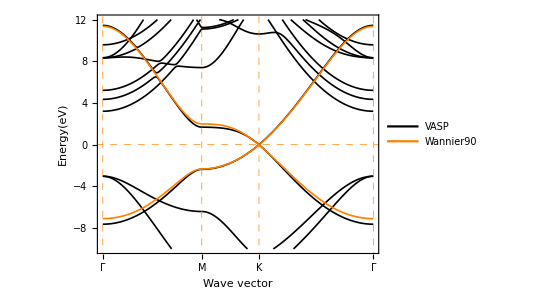

```mathematica
legend=LineLegend[{Black,Orange},{"VASP","Wannier90"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->0];
fig=Show[DFTfig,Wannier90ds[5],Legended[{},Placed[legend,{0.84,0.45}]]]
```

```mathematica
Export["wannier90Band.png",fig,ImageResolution->1000]
```

wannier90Band.png

```mathematica
hopping=Normal[dsLattice[4]];
Position[hopping,{0,0,0}]
Position[hopping,{1,0,0}]
Position[hopping,{1,1,0}]
Position[hopping,{0,1,0}]
Position[hopping,{-1,0,0}]
Position[hopping,{-1,-1,0}]
Position[hopping,{0,-1,0}]
```

{{166}}

{{184}}

{{185}}

{{167}}

{{148}}

{{147}}

{{165}}

```mathematica
h=Normal[dsLattice[6]];
h[[166]]//TraditionalForm
h[[184]]//TraditionalForm
h[[185]]//TraditionalForm
h[[167]]//TraditionalForm
h[[148]]//TraditionalForm
h[[147]]//TraditionalForm
h[[165]]//TraditionalForm
```

(-1.27709 | -2.82749
-2.82749 | -1.27709)

(0.239801 ⅇ^(ⅈ (1.23211 kx-2.13409 ky)) | -0.004839 ⅇ^(ⅈ (1.23211 kx-2.13409 ky))
-2.82749 ⅇ^(ⅈ (1.23211 kx-2.13409 ky)) | 0.2398 ⅇ^(ⅈ (1.23211 kx-2.13409 ky)))

(0.2398 ⅇ^((0.+2.46423 ⅈ) kx) | -0.215067 ⅇ^((0.+2.46423 ⅈ) kx)
-0.215067 ⅇ^((0.+2.46423 ⅈ) kx) | 0.239801 ⅇ^((0.+2.46423 ⅈ) kx))

(0.239801 ⅇ^(ⅈ (1.23211 kx+2.13409 ky)) | -2.82749 ⅇ^(ⅈ (1.23211 kx+2.13409 ky))
-0.004839 ⅇ^(ⅈ (1.23211 kx+2.13409 ky)) | 0.2398 ⅇ^(ⅈ (1.23211 kx+2.13409 ky)))

(0.239801 ⅇ^(ⅈ (2.13409 ky-1.23211 kx)) | -2.82749 ⅇ^(ⅈ (2.13409 ky-1.23211 kx))
-0.004839 ⅇ^(ⅈ (2.13409 ky-1.23211 kx)) | 0.2398 ⅇ^(ⅈ (2.13409 ky-1.23211 kx)))

(0.2398 ⅇ^((0.-2.46423 ⅈ) kx) | -0.215067 ⅇ^((0.-2.46423 ⅈ) kx)
-0.215067 ⅇ^((0.-2.46423 ⅈ) kx) | 0.239801 ⅇ^((0.-2.46423 ⅈ) kx))

(0.239801 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky)) | -0.004839 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky))
-2.82749 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky)) | 0.2398 ⅇ^(ⅈ (-1.23211 kx-2.13409 ky)))